```mathematica
translate[codon_]:=Which[codon=="GCT"||codon=="GCC"||codon=="GCA"||codon=="GCG","A",codon=="CGT"||codon=="CGC"||codon=="CGA"||codon=="CGG"||codon=="AGA"||codon=="AGG","R",codon=="AAC"||codon=="AAT","N",codon=="GAT"||codon=="GAC","D",codon=="TGT"||codon=="TGC","C",codon=="CAA"||codon=="CAG","Q",codon=="GAA"||codon=="GAG","E",codon=="GGT"||codon=="GGC"||codon=="GGA"||codon=="GGG","G",codon=="CAT"||codon=="CAC","H",codon=="ATT"||codon=="ATC"||codon=="ATA","I",codon=="TTA"||codon=="TTG"||codon=="CTT"||codon=="CTC"||codon=="CTA"||codon=="CTG","L",codon=="AAA"||codon=="AAG","K",codon=="ATG","M",codon=="TTT"||codon=="TTC","F",codon=="CCT"||codon=="CCC"||codon=="CCA"||codon=="CCG","P",codon=="TCT"||codon=="TCC"||codon=="TCA"||codon=="TCG"||codon=="AGT"||codon=="AGC","S",codon=="ACT"||codon=="ACC"||codon=="ACA"||codon=="ACG","T",codon=="TGG","W",codon=="TAT"||codon=="TAC","Y",codon=="GTT"||codon=="GTC"||codon=="GTA"||codon=="GTG","V"]

getcomplement[base_]:=Which[base=="G","C",base=="C","G",base=="T","A",base=="A","T"]

reversecomplement[sequence_]:=Module[{temp1,complement},

temp1=Characters[sequence];

complement=Table[getcomplement[temp1[[i]]],{i,1,Length[temp1]}];

StringJoin[Reverse[complement]]

]

primerparams[sequence_,annealingportion_,mismatch_]:=Module[{n,g,c,gc},

n=StringLength[sequence];

g=StringCount[sequence,"G"];

c=StringCount[sequence,"C"];

gc=(g+c)/n*100.0;

(*Print[TableForm[{{"Length","%GC","Tm"},{n,gc,81.5+0.41*gc-(675.0/n)-mismatch/42*100.}}]];*)

{n,gc,81.5+0.41*gc-(675.0/n)-mismatch/42*100.}

]

Tmscore[Tm_]:=Piecewise[{{2,Tm≥78.0&&Tm<82.0},{(Tm-77.0)+1,Tm<78.0},{-1*(Tm-82.0)+2,Tm≥82.0}}]
```

### Open an external Python process to calculate hairpin Tms

```mathematica
Tmcounter=0;

pythonpath=StartProcess[{path,"-i"}];

cmd="import primer3";
Pause[0.001];
WriteLine[pythonpath,cmd];

calcHairpin[sequence_]:=(

Tmcounternew=Tmcounter+1;

path="/Library/Frameworks/Python.framework/Versions/2.7/bin/python";

If[Tmcounternew==500,

(KillProcess[pythonpath];

pythonpath=StartProcess[{path,"-i"}];

cmd="import primer3";
Pause[0.001];
WriteLine[pythonpath,cmd];

Tmcounternew=0)];

cmd=StringJoin["primer3.calcHairpin('",sequence,"').tm"];
Pause[0.001];

WriteLine[pythonpath,cmd];

Pause[0.05];

out=ReadString[pythonpath,EndOfBuffer];

Tmcounter=Tmcounternew;

out)
```

```mathematica
calcHairpin["GCACATTCTGTGGGCTTTGGGCAAGCACATAAAATGCC"]
```

58.19360163176441

```mathematica
alanine={"GCT","GCC","GCA","GCG"};

arginine={"CGT","CGC","CGA","CGG","AGA","AGG"};

asparagine={"AAC","AAT","TAA"};

aspartate={"GAT","GAC"};

cysteine={"TGT","TGC"};

glutamine={"CAA","CAG"};

glutamate={"GAA","GAG"};

glycine={"GGT","GGC","GGA","GGG"};

histidine={"CAT","CAC"};

isoleucine={"ATT","ATC","ATA"};

leucine={"TTA","TTG","CTT","CTC","CTA","CTG"};

lysine={"AAA","AAG"};

methionine={"ATG"};

phenylalanine={"TTT","TTC"};

proline={"CCT","CCC","CCA","CCG"};

serine={"TCT","TCC","TCA","TCG","AGT","AGC"};

threonine={"ACT","ACC","ACA","ACG"};

tryptophan={"TGG"};

tyrosine={"TAT","TAC"};

valine={"GTT","GTC","GTA","GTG"};
```

```mathematica
pafAsequence="AGAAATAATTTTGTTTAACTTTAAGAAGGAGATATACATATGCAAAAAACGAATGCTGTACCAAGACCTAAACTTGTGGTAGGACTGGTAGTTGATCAGATGAGATGGGATTATCTTTACCGTTATTATAGCAAGTATGGTGAAGGAGGTTTTAAGAGAATGCTGAATACCGGGTATTCGTTAAATAATGTTCATATAGACTATGTACCTACAGTAACTGCAATCGGACATACTTCAATTTTTACAGGTTCTGTTCCCTCCATCCACGGAATTGCAGGAAACGATTGGTATGATAAAGAATTAGGGAAAAGTGTTTACTGTACATCTGATGAAACAGTACAACCGGTAGGAACTACTTCTAACTCGGTTGGACAACATTCACCAAGAAACCTTTGGTCTACTACGGTAACAGATCAGCTAGGTTTGGCAACAAACTTTACTTCTAAGGTTGTGGGGGTCTCTCTGAAAGACAGAGCATCAATTCTGCCTGCAGGGCACAACCCAACAGGAGCATTTTGGTTCGATGATACTACAGGTAAATTCATTACCAGTACATATTATACTAAAGAATTACCTAAATGGGTAAACGACTTTAATAATAAAAATGTTCCGGCTCAGTTGGTAGCTAATGGCTGGAATACACTATTGCCCATTAATCAGTATACAGAAAGCTCAGAAGATAATGTGGAATGGGAAGGTTTATTAGGGAGTAAAAAAACACCTACATTCCCTTATACAGATCTGGCTAAAGATTATGAAGCTAAAAAAGGATTAATCCGTACTACACCATTTGGAAATACCTTAACTCTTCAGATGGCAGATGCTGCAATTGATGGTAACCAAATGGGAGTTGATGATATTACTGACTTCCTTACAGTAAACCTTGCTTCAACGGATTATGTTGGACACAACTTTGGTCCAAACTCTATAGAAGTTGAGGATACTTATCTGAGATTAGACAGAGATTTGGCTGACTTCTTCAATAACCTTGATAAAAAAGTTGGAAAAGGAAACTACCTTGTATTCCTTTCTGCGGATCATGGCGCTGCACATTCTGTGGGCTTTATGCAAGCACATAAAATGCCAACAGGCTTCTTTGTAGAAGATATGAAAAAAGAAATGAACGCTAAGCTGAAGCAAAAATTCGGTGCTGATAATATAATTGCAGCTGCGATGAACTATCAGGTTTATTTCGACAGAAAGGTTTTAGCAGACAGCAAATTAGAATTGGATGACGTAAGAGATTATGTAATGACAGAACTTAAAAAAGAGCCATCAGTTCTTTATGTTCTTAGCACGGATGAAATCTGGGAATCGTCTATTCCGGAACCGATAAAGTCCAGAGTAATCAATGGTTATAACTGGAAAAGAAGCGGAGATATTCAGATCATTTCTAAAGACGGATATCTTTCAGCATATTCCAAAAAAGGGACAACACACAGTGTATGGAACTCTTATGATTCACATATTCCTTTACTCTTTATGGGGTGGGGTATCAAACAGGGAGAGTCCAATCAGCCATACCATATGACGGATATTGCACCAACTGTTTCATCATTACTTAAAATTCAGTTCCCTAGTGGTGCTGTAGGTAAACCAATTACCGAAGTTATAGGAAGAGGAGGAGGGTCTGGGGGAGGAGGCAGTGGCATGGTGAGCAAG";

pafAcodons=Partition[Characters[pafAsequence],3];
```

```mathematica
(* translate *)

translation=Table[{i,StringJoin["Res ",ToString[i*3-2]],StringJoin[pafAcodons[[i]]],Style[translate[StringJoin[pafAcodons[[i]]]],Bold]},{i,1,Length[pafAcodons]}]
```

{{1,Res 1,AGA,R},{2,Res 4,AAT,N},{3,Res 7,AAT,N},{4,Res 10,TTT,F},{5,Res 13,GTT,V},{6,Res 16,TAA,Null},{7,Res 19,CTT,L},{8,Res 22,TAA,Null},{9,Res 25,GAA,E},{10,Res 28,GGA,G},{11,Res 31,GAT,D},{12,Res 34,ATA,I},{13,Res 37,CAT,H},{14,Res 40,ATG,M},{15,Res 43,CAA,Q},{16,Res 46,AAA,K},{17,Res 49,ACG,T},{18,Res 52,AAT,N},{19,Res 55,GCT,A},{20,Res 58,GTA,V},{21,Res 61,CCA,P},{22,Res 64,AGA,R},{23,Res 67,CCT,P},{24,Res 70,AAA,K},{25,Res 73,CTT,L},{26,Res 76,GTG,V},{27,Res 79,GTA,V},{28,Res 82,GGA,G},{29,Res 85,CTG,L},{30,Res 88,GTA,V},{31,Res 91,GTT,V},{32,Res 94,GAT,D},{33,Res 97,CAG,Q},{34,Res 100,ATG,M},{35,Res 103,AGA,R},{36,Res 106,TGG,W},{37,Res 109,GAT,D},{38,Res 112,TAT,Y},{39,Res 115,CTT,L},{40,Res 118,TAC,Y},{41,Res 121,CGT,R},{42,Res 124,TAT,Y},{43,Res 127,TAT,Y},{44,Res 130,AGC,S},{45,Res 133,AAG,K},{46,Res 136,TAT,Y},{47,Res 139,GGT,G},{48,Res 142,GAA,E},{49,Res 145,GGA,G},{50,Res 148,GGT,G},{51,Res 151,TTT,F},{52,Res 154,AAG,K},{53,Res 157,AGA,R},{54,Res 160,ATG,M},{55,Res 163,CTG,L},{56,Res 166,AAT,N},{57,Res 169,ACC,T},{58,Res 172,GGG,G},{59,Res 175,TAT,Y},{60,Res 178,TCG,S},{61,Res 181,TTA,L},{62,Res 184,AAT,N},{63,Res 187,AAT,N},{64,Res 190,GTT,V},{65,Res 193,CAT,H},{66,Res 196,ATA,I},{67,Res 199,GAC,D},{68,Res 202,TAT,Y},{69,Res 205,GTA,V},{70,Res 208,CCT,P},{71,Res 211,ACA,T},{72,Res 214,GTA,V},{73,Res 217,ACT,T},{74,Res 220,GCA,A},{75,Res 223,ATC,I},{76,Res 226,GGA,G},{77,Res 229,CAT,H},{78,Res 232,ACT,T},{79,Res 235,TCA,S},{80,Res 238,ATT,I},{81,Res 241,TTT,F},{82,Res 244,ACA,T},{83,Res 247,GGT,G},{84,Res 250,TCT,S},{85,Res 253,GTT,V},{86,Res 256,CCC,P},{87,Res 259,TCC,S},{88,Res 262,ATC,I},{89,Res 265,CAC,H},{90,Res 268,GGA,G},{91,Res 271,ATT,I},{92,Res 274,GCA,A},{93,Res 277,GGA,G},{94,Res 280,AAC,N},{95,Res 283,GAT,D},{96,Res 286,TGG,W},{97,Res 289,TAT,Y},{98,Res 292,GAT,D},{99,Res 295,AAA,K},{100,Res 298,GAA,E},{101,Res 301,TTA,L},{102,Res 304,GGG,G},{103,Res 307,AAA,K},{104,Res 310,AGT,S},{105,Res 313,GTT,V},{106,Res 316,TAC,Y},{107,Res 319,TGT,C},{108,Res 322,ACA,T},{109,Res 325,TCT,S},{110,Res 328,GAT,D},{111,Res 331,GAA,E},{112,Res 334,ACA,T},{113,Res 337,GTA,V},{114,Res 340,CAA,Q},{115,Res 343,CCG,P},{116,Res 346,GTA,V},{117,Res 349,GGA,G},{118,Res 352,ACT,T},{119,Res 355,ACT,T},{120,Res 358,TCT,S},{121,Res 361,AAC,N},{122,Res 364,TCG,S},{123,Res 367,GTT,V},{124,Res 370,GGA,G},{125,Res 373,CAA,Q},{126,Res 376,CAT,H},{127,Res 379,TCA,S},{128,Res 382,CCA,P},{129,Res 385,AGA,R},{130,Res 388,AAC,N},{131,Res 391,CTT,L},{132,Res 394,TGG,W},{133,Res 397,TCT,S},{134,Res 400,ACT,T},{135,Res 403,ACG,T},{136,Res 406,GTA,V},{137,Res 409,ACA,T},{138,Res 412,GAT,D},{139,Res 415,CAG,Q},{140,Res 418,CTA,L},{141,Res 421,GGT,G},{142,Res 424,TTG,L},{143,Res 427,GCA,A},{144,Res 430,ACA,T},{145,Res 433,AAC,N},{146,Res 436,TTT,F},{147,Res 439,ACT,T},{148,Res 442,TCT,S},{149,Res 445,AAG,K},{150,Res 448,GTT,V},{151,Res 451,GTG,V},{152,Res 454,GGG,G},{153,Res 457,GTC,V},{154,Res 460,TCT,S},{155,Res 463,CTG,L},{156,Res 466,AAA,K},{157,Res 469,GAC,D},{158,Res 472,AGA,R},{159,Res 475,GCA,A},{160,Res 478,TCA,S},{161,Res 481,ATT,I},{162,Res 484,CTG,L},{163,Res 487,CCT,P},{164,Res 490,GCA,A},{165,Res 493,GGG,G},{166,Res 496,CAC,H},{167,Res 499,AAC,N},{168,Res 502,CCA,P},{169,Res 505,ACA,T},{170,Res 508,GGA,G},{171,Res 511,GCA,A},{172,Res 514,TTT,F},{173,Res 517,TGG,W},{174,Res 520,TTC,F},{175,Res 523,GAT,D},{176,Res 526,GAT,D},{177,Res 529,ACT,T},{178,Res 532,ACA,T},{179,Res 535,GGT,G},{180,Res 538,AAA,K},{181,Res 541,TTC,F},{182,Res 544,ATT,I},{183,Res 547,ACC,T},{184,Res 550,AGT,S},{185,Res 553,ACA,T},{186,Res 556,TAT,Y},{187,Res 559,TAT,Y},{188,Res 562,ACT,T},{189,Res 565,AAA,K},{190,Res 568,GAA,E},{191,Res 571,TTA,L},{192,Res 574,CCT,P},{193,Res 577,AAA,K},{194,Res 580,TGG,W},{195,Res 583,GTA,V},{196,Res 586,AAC,N},{197,Res 589,GAC,D},{198,Res 592,TTT,F},{199,Res 595,AAT,N},{200,Res 598,AAT,N},{201,Res 601,AAA,K},{202,Res 604,AAT,N},{203,Res 607,GTT,V},{204,Res 610,CCG,P},{205,Res 613,GCT,A},{206,Res 616,CAG,Q},{207,Res 619,TTG,L},{208,Res 622,GTA,V},{209,Res 625,GCT,A},{210,Res 628,AAT,N},{211,Res 631,GGC,G},{212,Res 634,TGG,W},{213,Res 637,AAT,N},{214,Res 640,ACA,T},{215,Res 643,CTA,L},{216,Res 646,TTG,L},{217,Res 649,CCC,P},{218,Res 652,ATT,I},{219,Res 655,AAT,N},{220,Res 658,CAG,Q},{221,Res 661,TAT,Y},{222,Res 664,ACA,T},{223,Res 667,GAA,E},{224,Res 670,AGC,S},{225,Res 673,TCA,S},{226,Res 676,GAA,E},{227,Res 679,GAT,D},{228,Res 682,AAT,N},{229,Res 685,GTG,V},{230,Res 688,GAA,E},{231,Res 691,TGG,W},{232,Res 694,GAA,E},{233,Res 697,GGT,G},{234,Res 700,TTA,L},{235,Res 703,TTA,L},{236,Res 706,GGG,G},{237,Res 709,AGT,S},{238,Res 712,AAA,K},{239,Res 715,AAA,K},{240,Res 718,ACA,T},{241,Res 721,CCT,P},{242,Res 724,ACA,T},{243,Res 727,TTC,F},{244,Res 730,CCT,P},{245,Res 733,TAT,Y},{246,Res 736,ACA,T},{247,Res 739,GAT,D},{248,Res 742,CTG,L},{249,Res 745,GCT,A},{250,Res 748,AAA,K},{251,Res 751,GAT,D},{252,Res 754,TAT,Y},{253,Res 757,GAA,E},{254,Res 760,GCT,A},{255,Res 763,AAA,K},{256,Res 766,AAA,K},{257,Res 769,GGA,G},{258,Res 772,TTA,L},{259,Res 775,ATC,I},{260,Res 778,CGT,R},{261,Res 781,ACT,T},{262,Res 784,ACA,T},{263,Res 787,CCA,P},{264,Res 790,TTT,F},{265,Res 793,GGA,G},{266,Res 796,AAT,N},{267,Res 799,ACC,T},{268,Res 802,TTA,L},{269,Res 805,ACT,T},{270,Res 808,CTT,L},{271,Res 811,CAG,Q},{272,Res 814,ATG,M},{273,Res 817,GCA,A},{274,Res 820,GAT,D},{275,Res 823,GCT,A},{276,Res 826,GCA,A},{277,Res 829,ATT,I},{278,Res 832,GAT,D},{279,Res 835,GGT,G},{280,Res 838,AAC,N},{281,Res 841,CAA,Q},{282,Res 844,ATG,M},{283,Res 847,GGA,G},{284,Res 850,GTT,V},{285,Res 853,GAT,D},{286,Res 856,GAT,D},{287,Res 859,ATT,I},{288,Res 862,ACT,T},{289,Res 865,GAC,D},{290,Res 868,TTC,F},{291,Res 871,CTT,L},{292,Res 874,ACA,T},{293,Res 877,GTA,V},{294,Res 880,AAC,N},{295,Res 883,CTT,L},{296,Res 886,GCT,A},{297,Res 889,TCA,S},{298,Res 892,ACG,T},{299,Res 895,GAT,D},{300,Res 898,TAT,Y},{301,Res 901,GTT,V},{302,Res 904,GGA,G},{303,Res 907,CAC,H},{304,Res 910,AAC,N},{305,Res 913,TTT,F},{306,Res 916,GGT,G},{307,Res 919,CCA,P},{308,Res 922,AAC,N},{309,Res 925,TCT,S},{310,Res 928,ATA,I},{311,Res 931,GAA,E},{312,Res 934,GTT,V},{313,Res 937,GAG,E},{314,Res 940,GAT,D},{315,Res 943,ACT,T},{316,Res 946,TAT,Y},{317,Res 949,CTG,L},{318,Res 952,AGA,R},{319,Res 955,TTA,L},{320,Res 958,GAC,D},{321,Res 961,AGA,R},{322,Res 964,GAT,D},{323,Res 967,TTG,L},{324,Res 970,GCT,A},{325,Res 973,GAC,D},{326,Res 976,TTC,F},{327,Res 979,TTC,F},{328,Res 982,AAT,N},{329,Res 985,AAC,N},{330,Res 988,CTT,L},{331,Res 991,GAT,D},{332,Res 994,AAA,K},{333,Res 997,AAA,K},{334,Res 1000,GTT,V},{335,Res 1003,GGA,G},{336,Res 1006,AAA,K},{337,Res 1009,GGA,G},{338,Res 1012,AAC,N},{339,Res 1015,TAC,Y},{340,Res 1018,CTT,L},{341,Res 1021,GTA,V},{342,Res 1024,TTC,F},{343,Res 1027,CTT,L},{344,Res 1030,TCT,S},{345,Res 1033,GCG,A},{346,Res 1036,GAT,D},{347,Res 1039,CAT,H},{348,Res 1042,GGC,G},{349,Res 1045,GCT,A},{350,Res 1048,GCA,A},{351,Res 1051,CAT,H},{352,Res 1054,TCT,S},{353,Res 1057,GTG,V},{354,Res 1060,GGC,G},{355,Res 1063,TTT,F},{356,Res 1066,ATG,M},{357,Res 1069,CAA,Q},{358,Res 1072,GCA,A},{359,Res 1075,CAT,H},{360,Res 1078,AAA,K},{361,Res 1081,ATG,M},{362,Res 1084,CCA,P},{363,Res 1087,ACA,T},{364,Res 1090,GGC,G},{365,Res 1093,TTC,F},{366,Res 1096,TTT,F},{367,Res 1099,GTA,V},{368,Res 1102,GAA,E},{369,Res 1105,GAT,D},{370,Res 1108,ATG,M},{371,Res 1111,AAA,K},{372,Res 1114,AAA,K},{373,Res 1117,GAA,E},{374,Res 1120,ATG,M},{375,Res 1123,AAC,N},{376,Res 1126,GCT,A},{377,Res 1129,AAG,K},{378,Res 1132,CTG,L},{379,Res 1135,AAG,K},{380,Res 1138,CAA,Q},{381,Res 1141,AAA,K},{382,Res 1144,TTC,F},{383,Res 1147,GGT,G},{384,Res 1150,GCT,A},{385,Res 1153,GAT,D},{386,Res 1156,AAT,N},{387,Res 1159,ATA,I},{388,Res 1162,ATT,I},{389,Res 1165,GCA,A},{390,Res 1168,GCT,A},{391,Res 1171,GCG,A},{392,Res 1174,ATG,M},{393,Res 1177,AAC,N},{394,Res 1180,TAT,Y},{395,Res 1183,CAG,Q},{396,Res 1186,GTT,V},{397,Res 1189,TAT,Y},{398,Res 1192,TTC,F},{399,Res 1195,GAC,D},{400,Res 1198,AGA,R},{401,Res 1201,AAG,K},{402,Res 1204,GTT,V},{403,Res 1207,TTA,L},{404,Res 1210,GCA,A},{405,Res 1213,GAC,D},{406,Res 1216,AGC,S},{407,Res 1219,AAA,K},{408,Res 1222,TTA,L},{409,Res 1225,GAA,E},{410,Res 1228,TTG,L},{411,Res 1231,GAT,D},{412,Res 1234,GAC,D},{413,Res 1237,GTA,V},{414,Res 1240,AGA,R},{415,Res 1243,GAT,D},{416,Res 1246,TAT,Y},{417,Res 1249,GTA,V},{418,Res 1252,ATG,M},{419,Res 1255,ACA,T},{420,Res 1258,GAA,E},{421,Res 1261,CTT,L},{422,Res 1264,AAA,K},{423,Res 1267,AAA,K},{424,Res 1270,GAG,E},{425,Res 1273,CCA,P},{426,Res 1276,TCA,S},{427,Res 1279,GTT,V},{428,Res 1282,CTT,L},{429,Res 1285,TAT,Y},{430,Res 1288,GTT,V},{431,Res 1291,CTT,L},{432,Res 1294,AGC,S},{433,Res 1297,ACG,T},{434,Res 1300,GAT,D},{435,Res 1303,GAA,E},{436,Res 1306,ATC,I},{437,Res 1309,TGG,W},{438,Res 1312,GAA,E},{439,Res 1315,TCG,S},{440,Res 1318,TCT,S},{441,Res 1321,ATT,I},{442,Res 1324,CCG,P},{443,Res 1327,GAA,E},{444,Res 1330,CCG,P},{445,Res 1333,ATA,I},{446,Res 1336,AAG,K},{447,Res 1339,TCC,S},{448,Res 1342,AGA,R},{449,Res 1345,GTA,V},{450,Res 1348,ATC,I},{451,Res 1351,AAT,N},{452,Res 1354,GGT,G},{453,Res 1357,TAT,Y},{454,Res 1360,AAC,N},{455,Res 1363,TGG,W},{456,Res 1366,AAA,K},{457,Res 1369,AGA,R},{458,Res 1372,AGC,S},{459,Res 1375,GGA,G},{460,Res 1378,GAT,D},{461,Res 1381,ATT,I},{462,Res 1384,CAG,Q},{463,Res 1387,ATC,I},{464,Res 1390,ATT,I},{465,Res 1393,TCT,S},{466,Res 1396,AAA,K},{467,Res 1399,GAC,D},{468,Res 1402,GGA,G},{469,Res 1405,TAT,Y},{470,Res 1408,CTT,L},{471,Res 1411,TCA,S},{472,Res 1414,GCA,A},{473,Res 1417,TAT,Y},{474,Res 1420,TCC,S},{475,Res 1423,AAA,K},{476,Res 1426,AAA,K},{477,Res 1429,GGG,G},{478,Res 1432,ACA,T},{479,Res 1435,ACA,T},{480,Res 1438,CAC,H},{481,Res 1441,AGT,S},{482,Res 1444,GTA,V},{483,Res 1447,TGG,W},{484,Res 1450,AAC,N},{485,Res 1453,TCT,S},{486,Res 1456,TAT,Y},{487,Res 1459,GAT,D},{488,Res 1462,TCA,S},{489,Res 1465,CAT,H},{490,Res 1468,ATT,I},{491,Res 1471,CCT,P},{492,Res 1474,TTA,L},{493,Res 1477,CTC,L},{494,Res 1480,TTT,F},{495,Res 1483,ATG,M},{496,Res 1486,GGG,G},{497,Res 1489,TGG,W},{498,Res 1492,GGT,G},{499,Res 1495,ATC,I},{500,Res 1498,AAA,K},{501,Res 1501,CAG,Q},{502,Res 1504,GGA,G},{503,Res 1507,GAG,E},{504,Res 1510,TCC,S},{505,Res 1513,AAT,N},{506,Res 1516,CAG,Q},{507,Res 1519,CCA,P},{508,Res 1522,TAC,Y},{509,Res 1525,CAT,H},{510,Res 1528,ATG,M},{511,Res 1531,ACG,T},{512,Res 1534,GAT,D},{513,Res 1537,ATT,I},{514,Res 1540,GCA,A},{515,Res 1543,CCA,P},{516,Res 1546,ACT,T},{517,Res 1549,GTT,V},{518,Res 1552,TCA,S},{519,Res 1555,TCA,S},{520,Res 1558,TTA,L},{521,Res 1561,CTT,L},{522,Res 1564,AAA,K},{523,Res 1567,ATT,I},{524,Res 1570,CAG,Q},{525,Res 1573,TTC,F},{526,Res 1576,CCT,P},{527,Res 1579,AGT,S},{528,Res 1582,GGT,G},{529,Res 1585,GCT,A},{530,Res 1588,GTA,V},{531,Res 1591,GGT,G},{532,Res 1594,AAA,K},{533,Res 1597,CCA,P},{534,Res 1600,ATT,I},{535,Res 1603,ACC,T},{536,Res 1606,GAA,E},{537,Res 1609,GTT,V},{538,Res 1612,ATA,I},{539,Res 1615,GGA,G},{540,Res 1618,AGA,R},{541,Res 1621,GGA,G},{542,Res 1624,GGA,G},{543,Res 1627,GGG,G},{544,Res 1630,TCT,S},{545,Res 1633,GGG,G},{546,Res 1636,GGA,G},{547,Res 1639,GGA,G},{548,Res 1642,GGC,G},{549,Res 1645,AGT,S},{550,Res 1648,GGC,G},{551,Res 1651,ATG,M},{552,Res 1654,GTG,V},{553,Res 1657,AGC,S},{554,Res 1660,AAG,K}}

```mathematica
mutation={"G47A","N56G","V72G","T73G","T82G","S87G","I88G","I91G","V116G","T118G","T119G","S120G","N121G","S122G","W132G","Q139G","L140G","G141A","A143G","N145G","F146G","T147G","S154G","K156G","D157G","A159G","S160G","I161G","L162G","A164G","H166G","N167G","P168G","T169G","G170A","T177G","T178G","F181G","S184G","T185G","Y186G","K189G","V208G","Q220G","Y245G","G257A","T261G","T267G","D274G","A275G","I277G","D278G","G279A","N304G","F305G","I310G","E311G","V312G","Y316G","L317G","R318G","L319G","G348A","S352G","F355G","M356G","Q357G","H359G","K360G","V427G","S432G","P442G","I445G","K446G","Y469G","S504G","P515G","S518G","P533G","E536G","V537G"};
```

```mathematica
Length[mutation]
```

81

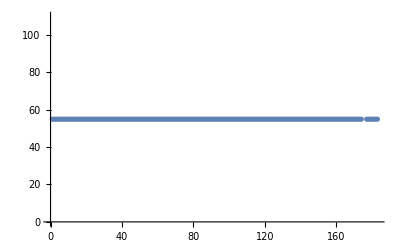

{G47A,{{CCGTTATTATAGCAAGTATGCTGAAGGAGGTTTTAAGAGAATG,{43,37.2093,78.6772},2.03013,54.8795},{CGTTATTATAGCAAGTATGCTGAAGGAGGTTTTAAGAGAATGC,{43,37.2093,78.6772},2.03013,54.8795},{CGTTATTATAGCAAGTATGCTGAAGGAGGTTTTAAGAGAATG,{42,35.7143,77.6905},1.97061,54.8795}}}

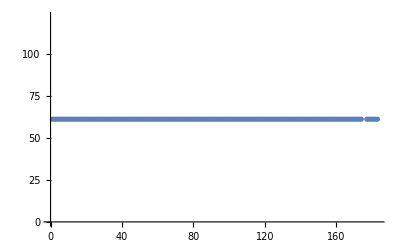

{N56G,{{GAGGTTTTAAGAGAATGCTGGGTACCGGGTATTCGTTAAATAATGTTC,{48,39.5833,78.9048},0.716837,61.1327},{GAGGTTTTAAGAGAATGCTGGGTACCGGGTATTCGTTAAATAATG,{45,40.,78.1381},0.716837,61.1327},{GGAGGTTTTAAGAGAATGCTGGGTACCGGGTATTCGTTAAATAATG,{46,41.3043,78.999},0.466837,61.1327}}}

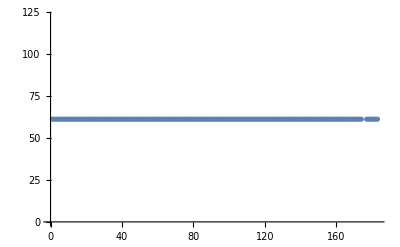

{V72G,{{GACTATGTACCTACAGGAACTGCAATCGGACATACTTC,{38,44.7368,79.698},0.675276,61.2989},{GACTATGTACCTACAGGAACTGCAATCGGACATAC,{35,45.7143,78.5762},0.675276,61.2989},{CTATGTACCTACAGGAACTGCAATCGGACATAC,{33,45.4545,77.3009},-0.0238578,61.2989}}}

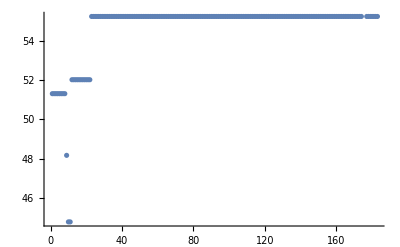

{T73G,{{GACTATGTACCTACAGTAGGTGCAATCGGACATACTTC,{38,44.7368,77.317},1.51065,55.2256},{CATATAGACTATGTACCTACAGTAGGTGCAATCGGACATACTTCAATTT,{49,36.7347,78.0238},0.943605,55.2256},{CATATAGACTATGTACCTACAGTAGGTGCAATCGGACATACTTCAATT,{48,37.5,78.0506},0.943605,55.2256}}}

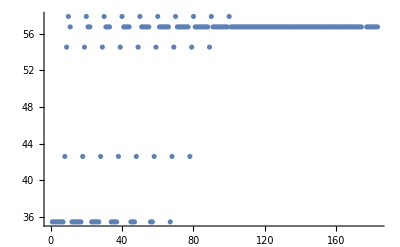

{T82G,{{CGGACATACTTCAATTTTTGGAGGTTCTGTTCCCTC,{36,44.4444,76.2103},2.21032,42.5915},{CGGACATACTTCAATTTTTGGAGGTTCTGTTCCCTCCATC,{40,45.,78.3131},1.81733,56.7307},{GACATACTTCAATTTTTGGAGGTTCTGTTCCCTCCATCCAC,{41,43.9024,78.2747},1.81733,56.7307}}}

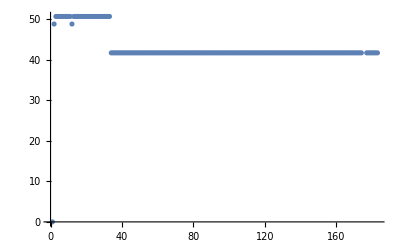

{S87G,{{CAGGTTCTGTTCCCGGCATCCACGGAATTGCAG,{33,57.5758,79.8896},3.34807,50.6077},{CAGGTTCTGTTCCCGGCATCCACGGAATTGCAGG,{34,58.8235,81.0028},3.09807,50.6077},{CAGGTTCTGTTCCCGGCATCCACGGAATTGC,{31,58.0645,78.7704},3.09807,50.6077}}}

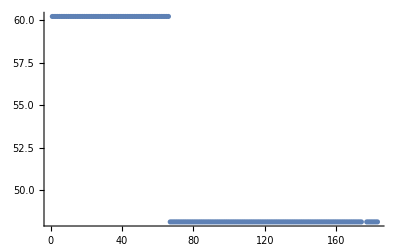

{I88G,{{ACAGGTTCTGTTCCCTCCGGCCACGGAATTGCAG,{34,58.8235,81.0028},2.9698,48.1208},{TACAGGTTCTGTTCCCTCCGGCCACGGAATTGCAGG,{36,58.3333,81.9048},2.7198,48.1208},{ACAGGTTCTGTTCCCTCCGGCCACGGAATTGCAGG,{35,60.,82.0524},2.66742,48.1208}}}

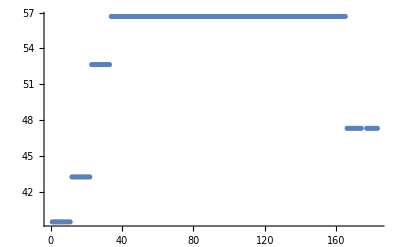

{I91G,{{CTCCATCCACGGAGGTGCAGGAAACGATTGG,{31,58.0645,78.7704},3.75,43.2489},{CTCCATCCACGGAGGTGCAGGAAACGATTG,{30,56.6667,77.4714},3.47143,43.2489},{CTCCATCCACGGAGGTGCAGGAAACGATTGGT,{32,56.25,78.7068},3.,43.2489}}}

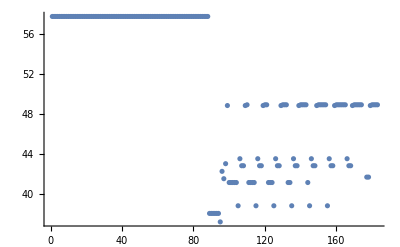

{V116G,{{CTGATGAAACAGTACAACCGGGAGGAACTACTTCTAAC,{38,44.7368,79.698},4.,38.0342},{CTGATGAAACAGTACAACCGGGAGGAACTACTTCTAACTC,{40,45.,80.694},2.4,38.0342},{CTGATGAAACAGTACAACCGGGAGGAACTACTTCTAACTCG,{41,46.3415,81.6556},2.11,38.0342}}}

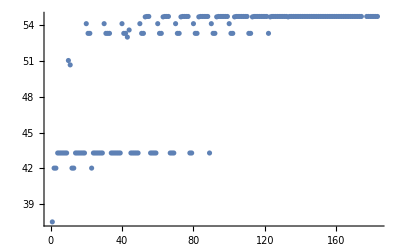

{T118G,{{CAGTACAACCGGTAGGAGGTACTTCTAACTCGG,{33,51.5152,77.4048},3.15476,43.2902},{GTACAACCGGTAGGAGGTACTTCTAACTCGGTTGGAC,{37,51.3514,79.5489},2.74648,53.0141},{CAACCGGTAGGAGGTACTTCTAACTCGGTTGG,{32,53.125,77.4256},2.50497,50.6825}}}

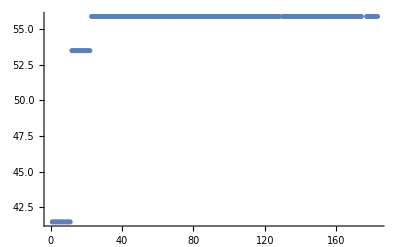

{T119G,{{CCGGTAGGAACTGGTTCTAACTCGGTTGGAC,{31,54.8387,77.4478},3.19777,41.475},{CCGGTAGGAACTGGTTCTAACTCGGTTGGACA,{32,53.125,77.4256},2.1756,41.475},{GTACAACCGGTAGGAACTGGTTCTAACTCGGTTGGAC,{37,51.3514,79.5489},2.02943,55.8823}}}

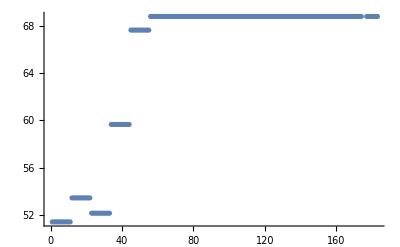

{S120G,{{CGGTAGGAACTACTGGTAACTCGGTTGGACAAC,{33,51.5152,77.4048},2.37298,52.1271},{CGGTAGGAACTACTGGTAACTCGGTTGGACAACA,{34,50.,77.3852},1.35337,52.1271},{CGGTAGGAACTACTGGTAACTCGGTTGGACAACAT,{35,48.5714,77.3667},1.08488,52.1271}}}

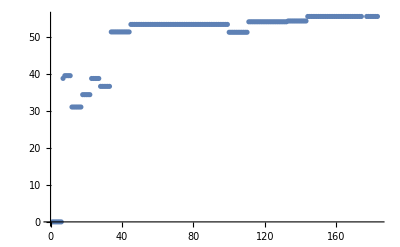

{N121G,{{GTAGGAACTACTTCTGGCTCGGTTGGACAACATTCAC,{37,48.6486,78.4408},3.15249,51.39},{GTAGGAACTACTTCTGGCTCGGTTGGACAACATTCACC,{38,50.,79.4749},2.90249,51.39},{CGGTAGGAACTACTTCTGGCTCGGTTGGACAACATTC,{37,51.3514,79.5489},2.64426,53.423}}}

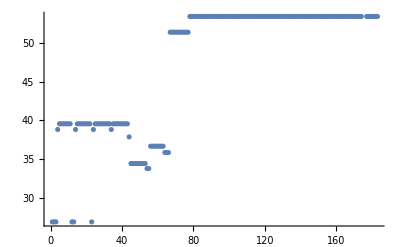

{S122G,{{GGAACTACTTCTAACGGGGTTGGACAACATTCACCAAG,{38,47.3684,78.396},3.75,37.8679},{TAGGAACTACTTCTAACGGGGTTGGACAACATTCACCAAG,{40,45.,78.3131},3.,35.8457},{AGGAACTACTTCTAACGGGGTTGGACAACATTCACCAAG,{39,46.1538,78.3535},3.,33.774}}}

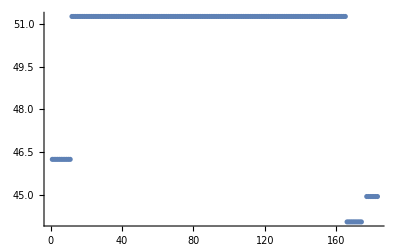

{W132G,{{CATTCACCAAGAAACCTTGGGTCTACTACGGTAACAG,{37,45.9459,79.7136},3.18384,51.2646},{CATTCACCAAGAAACCTTGGGTCTACTACGGTAAC,{35,45.7143,78.5762},3.18384,51.2646},{CACCAAGAAACCTTGGGTCTACTACGGTAACAGATC,{36,47.2222,79.7302},3.18384,51.2646}}}

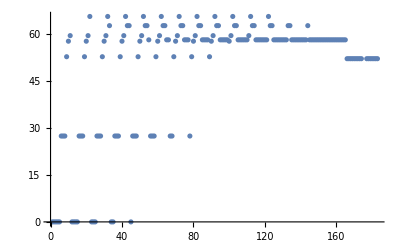

{Q139G,{{GTCTACTACGGTAACAGATGGGCTAGGTTTGGCAAC,{36,50.,78.4881},4.,27.3743},{CTACTACGGTAACAGATGGGCTAGGTTTGGCAAC,{34,50.,77.3852},3.38515,27.3743},{TCTACTACGGTAACAGATGGGCTAGGTTTGGCAAC,{35,48.5714,77.3667},2.36667,27.3743}}}

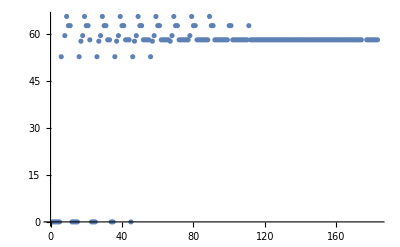

{L140G,{{CTACGGTAACAGATCAGGGAGGTTTGGCAACAAACTTTAC,{40,45.,78.3131},1.49075,58.037},{CGGTAACAGATCAGGGAGGTTTGGCAAC,{28,53.5714,74.5952},0.595238,0.},{TACTACGGTAACAGATCAGGGAGGTTTGGCAACAAACTTTAC,{42,42.8571,78.2381},0.490754,58.037}}}

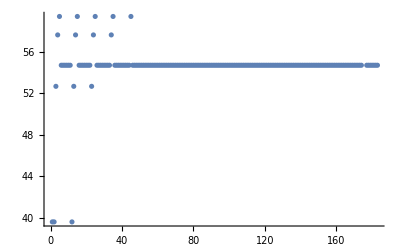

{G141A,{{CGGTAACAGATCAGCTAGCTTTGGCAACAAACTTTAC,{37,43.2432,78.6055},2.32859,54.6857},{GGTAACAGATCAGCTAGCTTTGGCAACAAACTTTACTTC,{39,41.0256,78.6319},2.07859,54.6857},{GTAACAGATCAGCTAGCTTTGGCAACAAACTTTACTTC,{38,39.4737,77.5401},1.86869,54.6857}}}

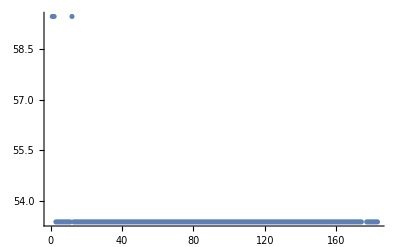

{A143G,{{GTAACAGATCAGCTAGGTTTGGGAACAAACTTTACTTCTAAG,{42,38.0952,78.6667},2.65363,53.3855},{CAGATCAGCTAGGTTTGGGAACAAACTTTACTTCTAAGG,{39,41.0256,78.6319},2.40363,53.3855},{CAGATCAGCTAGGTTTGGGAACAAACTTTACTTCTAAG,{38,39.4737,77.5401},2.19373,53.3855}}}

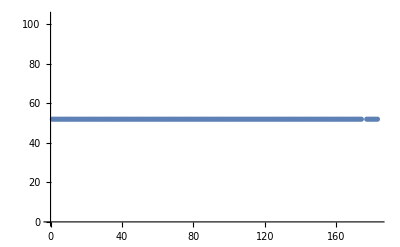

{N145G,{{GATCAGCTAGGTTTGGCAACAGGCTTTACTTCTAAGGTTG,{40,45.,78.3131},2.99499,52.02},{CAGCTAGGTTTGGCAACAGGCTTTACTTCTAAGGTTGTG,{39,46.1538,78.3535},2.99499,52.02},{GCTAGGTTTGGCAACAGGCTTTACTTCTAAGGTTGTGG,{38,47.3684,78.396},2.74499,52.02}}}

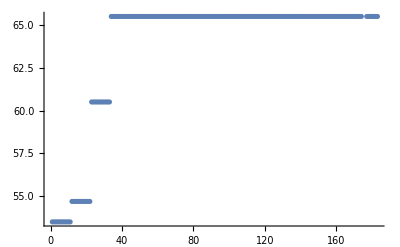

{F146G,{{GTTTGGCAACAAACGGTACTTCTAAGGTTGTGGGGG,{36,50.,78.4881},0.625342,60.4986},{GTTTGGCAACAAACGGTACTTCTAAGGTTGTGGGG,{35,48.5714,77.3667},-0.00799158,60.4986},{GCTAGGTTTGGCAACAAACGGTACTTCTAAGGTTGTGG,{38,47.3684,78.396},-0.624439,65.4978}}}

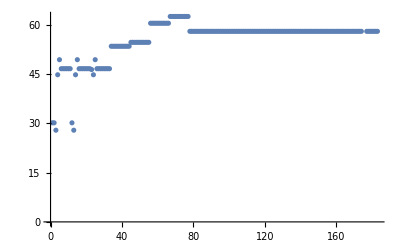

{T147G,{{GGCAACAAACTTTGGTTCTAAGGTTGTGGGGGTC,{34,50.,77.3852},3.13515,46.6533},{TGGCAACAAACTTTGGTTCTAAGGTTGTGGGGGTC,{35,48.5714,77.3667},2.36667,46.6533},{GGCAACAAACTTTGGTTCTAAGGTTGTGGGGG,{32,50.,76.1443},1.64435,46.6533}}}

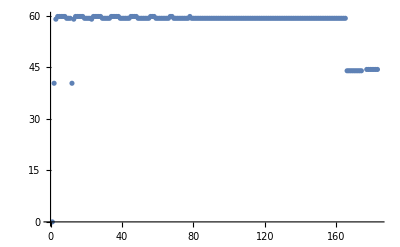

{S154G,{{CTAAGGTTGTGGGGGTCGGTCTGAAAGACAGAGCATC,{37,54.0541,80.657},1.17456,59.3018},{GTTGTGGGGGTCGGTCTGAAAGACAGAGCATC,{32,56.25,78.7068},1.17456,59.3018},{CTAAGGTTGTGGGGGTCGGTCTGAAAGACAGAG,{33,54.5455,78.6472},1.04192,59.8323}}}

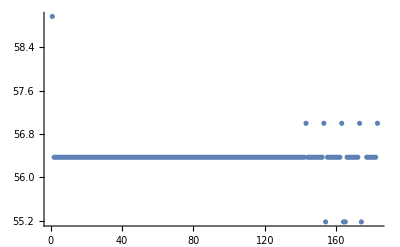

{K156G,{{GTTGTGGGGGTCTCTCTGGGAGACAGAGCATCAATTC,{37,54.0541,80.657},1.90655,56.3738},{GTGGGGGTCTCTCTGGGAGACAGAGCATCAATTCTG,{36,55.5556,80.7659},1.90655,56.3738},{GTGGGGGTCTCTCTGGGAGACAGAGCATCAATTC,{34,55.8824,79.7969},1.90655,56.3738}}}

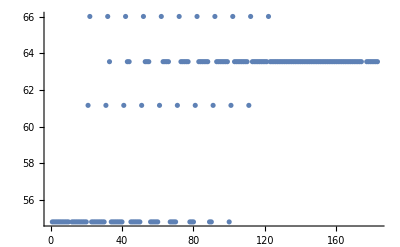

{D157G,{{GTGGGGGTCTCTCTGAAAGGCAGAGCATCAATTC,{34,52.9412,80.972},2.30391,54.7844},{GTGGGGGTCTCTCTGAAAGGCAGAGCATCAATTCTG,{36,52.7778,82.0079},2.29597,54.7844},{GGGGGTCTCTCTGAAAGGCAGAGCATCAATTCTG,{34,52.9412,80.972},2.05391,54.7844}}}

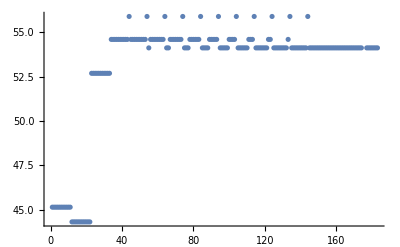

{A159G,{{CTGAAAGACAGAGGATCAATTCTGCCTGCAGG,{32,50.,78.5253},3.75,45.1337},{CTGAAAGACAGAGGATCAATTCTGCCTGCAG,{31,48.3871,77.1836},3.18356,45.1337},{CTCTGAAAGACAGAGGATCAATTCTGCCTGCAG,{33,48.4848,78.5433},2.82769,52.6892}}}

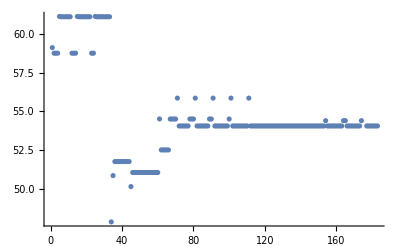

{S160G,{{CTGAAAGACAGAGCAGGAATTCTGCCTGCAGGGCAC,{36,55.5556,80.7659},3.05936,51.7626},{CTCTGAAAGACAGAGCAGGAATTCTGCCTGCAGGGC,{36,55.5556,80.7659},2.98558,51.0577},{CTCTGAAAGACAGAGCAGGAATTCTGCCTGCAGGG,{35,54.2857,79.7095},2.98558,51.0577}}}

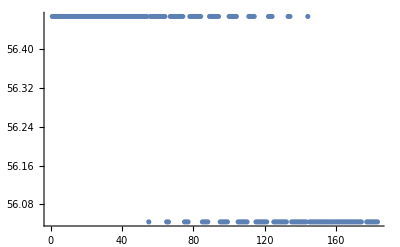

{I161G,{{CTGAAAGACAGAGCATCAGGTCTGCCTGCAGGGCAC,{36,58.3333,81.9048},1.88295,56.4682},{GAAAGACAGAGCATCAGGTCTGCCTGCAGGGCACAAC,{37,56.7568,81.7651},1.88295,56.4682},{GAAAGACAGAGCATCAGGTCTGCCTGCAGGGCAC,{34,58.8235,81.0028},1.88295,56.4682}}}

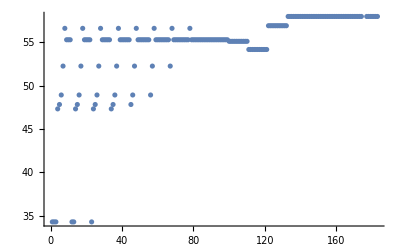

{L162G,{{GACAGAGCATCAATTGGGCCTGCAGGGCAC,{30,60.,78.8381},3.76794,48.9282},{CAGAGCATCAATTGGGCCTGCAGGGCAC,{28,60.7143,77.5238},3.29175,48.9282},{GACAGAGCATCAATTGGGCCTGCAGGGC,{28,60.7143,77.5238},3.27381,47.3237}}}

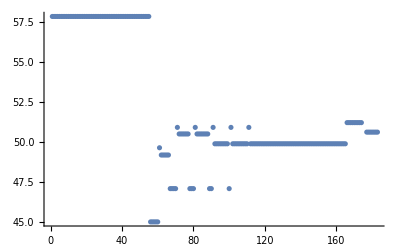

{A164G,{{GAGCATCAATTCTGCCTGGAGGGCACAACCCAAC,{34,55.8824,82.1779},3.82213,45.0226},{GAGCATCAATTCTGCCTGGAGGGCACAACCCA,{32,56.25,81.0878},3.,45.0226},{AGAGCATCAATTCTGCCTGGAGGGCACAACCCAAC,{35,54.2857,82.0905},2.90952,47.1017}}}

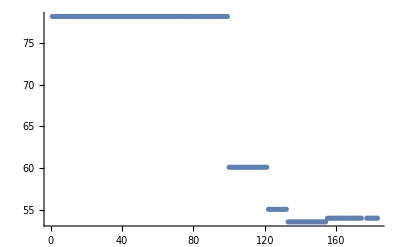

{H166G,{{GAGCATCAATTCTGCCTGCAGGGGGCAACCCAACAGGAGCATTTTG,{46,54.3478,84.3468},-1.94157,55.0191},{CAGAGCATCAATTCTGCCTGCAGGGGGCAACCCAACAGGAGCATTTTG,{48,54.1667,84.8839},-2.18149,53.5103},{GAGCATCAATTCTGCCTGCAGGGGGCAACCCAACAGGAGCATTTT,{45,53.3333,83.6048},-2.40954,55.0191}}}

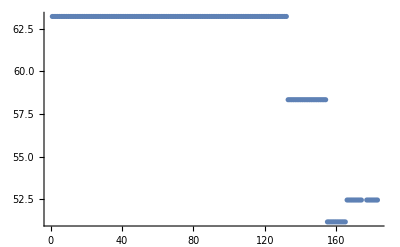

{N167G,{{CTGCCTGCAGGGCACGGCCCAACAGGAG,{28,71.4286,81.9167},0.197344,63.2106},{GCCTGCAGGGCACGGCCCAACAGGAG,{26,73.0769,80.7381},0.197344,63.2106},{GCCTGCAGGGCACGGCCCAACAGG,{24,75.,79.3631},-0.0526555,63.2106}}}

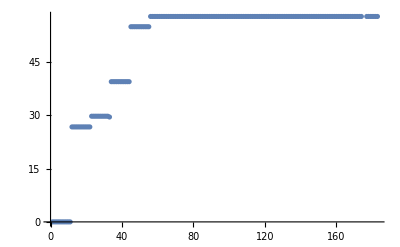

{P168G,{{CTGCAGGGCACAACGGAACAGGAGCATTTTGGTTC,{35,54.2857,79.7095},4.,29.7673},{CCTGCAGGGCACAACGGAACAGGAGCATTTTGGTTC,{36,55.5556,80.7659},3.75,39.491},{CCTGCAGGGCACAACGGAACAGGAGCATTTTG,{32,56.25,78.7068},3.75,39.491}}}

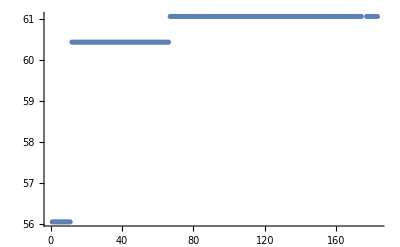

{T169G,{{GGGCACAACCCAGGAGGAGCATTTTGGTTC,{30,56.6667,77.4714},1.2083,56.0525},{GGGCACAACCCAGGAGGAGCATTTTGGTTCG,{31,58.0645,78.7704},0.986869,56.0525},{CTGCAGGGCACAACCCAGGAGGAGCATTTTGGTTC,{35,57.1429,80.881},0.888937,60.4443}}}

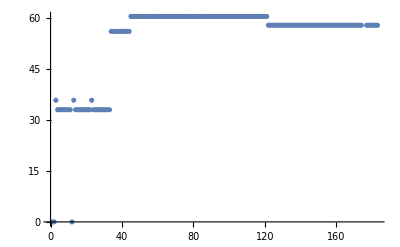

{G170A,{{GCACAACCCAACAGCAGCATTTTGGTTCGATG,{32,50.,78.5253},4.,33.0035},{GGCACAACCCAACAGCAGCATTTTGGTTCGATG,{33,51.5152,79.7857},3.75,33.0035},{CACAACCCAACAGCAGCATTTTGGTTCGATG,{31,48.3871,77.1836},3.18356,33.0035}}}

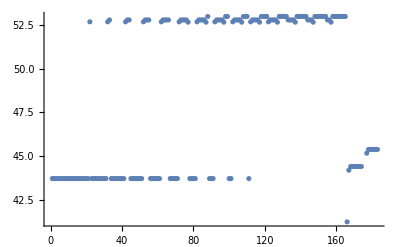

{T177G,{{GAGCATTTTGGTTCGATGATGGTACAGGTAAATTCATTACCAGTAC,{46,39.1304,78.1077},2.83612,52.6555},{CAGGAGCATTTTGGTTCGATGATGGTACAGGTAAATTCATTACCAG,{46,41.3043,78.999},2.80427,52.7829},{GGAGCATTTTGGTTCGATGATGGTACAGGTAAATTCATTACCAGTAC,{47,40.4255,78.9509},2.58612,52.6555}}}

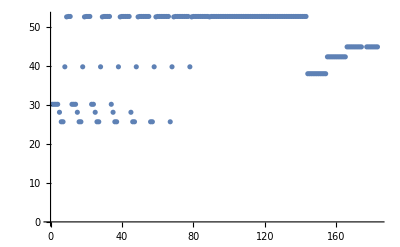

{T178G,{{AGGAGCATTTTGGTTCGATGATACTGGAGGTAAATTCATTACCAGTAC,{48,39.5833,78.9048},3.,38.0667},{GAGCATTTTGGTTCGATGATACTGGAGGTAAATTCATTACCAGTAC,{46,39.1304,78.1077},2.80427,52.7829},{GGAGCATTTTGGTTCGATGATACTGGAGGTAAATTCATTACCAGTAC,{47,40.4255,78.9509},2.55427,52.7829}}}

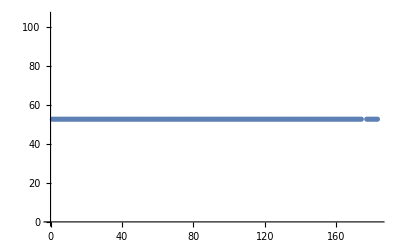

{F181G,{{GGTTCGATGATACTACAGGTAAAGGCATTACCAGTACATATTATAC,{46,36.9565,77.2164},1.77063,52.7829},{GTTCGATGATACTACAGGTAAAGGCATTACCAGTACATATTATAC,{45,35.5556,76.3159},1.12015,52.7829},{TGGTTCGATGATACTACAGGTAAAGGCATTACCAGTACATATTATAC,{47,36.1702,77.2062},1.01045,52.7829}}}

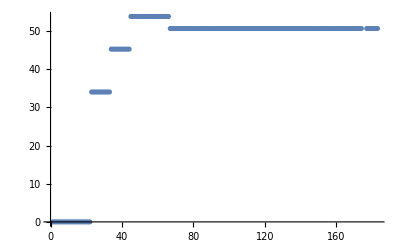

{S184G,{{GATACTACAGGTAAATTCATTACCGGTACATATTATACTAAAGAATTAC,{49,28.5714,77.0578},2.38052,50.7092},{CTACAGGTAAATTCATTACCGGTACATATTATACTAAAGAATTACC,{46,30.4348,76.9234},1.99609,50.7092},{CTACAGGTAAATTCATTACCGGTACATATTATACTAAAGAATTACCT,{47,29.7872,76.9701},1.29281,50.7092}}}

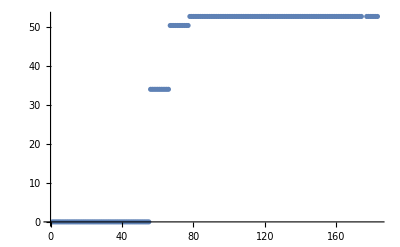

{T185G,{{CTACAGGTAAATTCATTACCAGTGGATATTATACTAAAGAATTACC,{46,30.4348,74.5424},-0.903283,52.7829},{CTACAGGTAAATTCATTACCAGTGGATATTATACTAAAGAATTACCT,{47,29.7872,74.5892},-1.60657,52.7829},{CTACAGGTAAATTCATTACCAGTGGATATTATACTAAAGAATTAC,{45,28.8889,73.5825},-1.61319,52.7829}}}

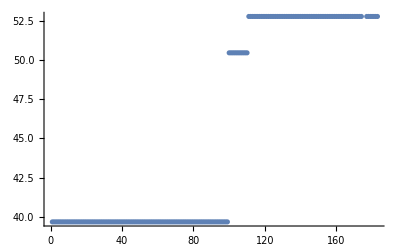

{Y186G,{{GTAAATTCATTACCAGTACAGGTTATACTAAAGAATTACCTAAATGGG,{48,31.25,75.4881},1.2381,39.6777},{GGTAAATTCATTACCAGTACAGGTTATACTAAAGAATTACCTAAATGGG,{49,32.6531,76.3503},1.23474,50.4624},{GGTAAATTCATTACCAGTACAGGTTATACTAAAGAATTACCTAAATGG,{48,31.25,75.4881},0.372496,50.4624}}}

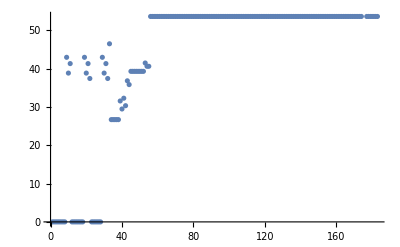

{K189G,{{CATTACCAGTACATATTATACTGGAGAATTACCTAAATGGGTAAACGAC,{49,34.6939,77.1871},1.78995,53.5885},{CATTACCAGTACATATTATACTGGAGAATTACCTAAATGGGTAAACG,{47,34.0426,76.3338},0.68671,53.5885},{CATTACCAGTACATATTATACTGGAGAATTACCTAAATGGGTAAAC,{46,32.6087,75.4337},0.0366179,53.5885}}}

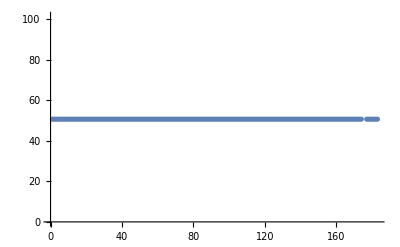

{V208G,{{GTTCCGGCTCAGTTGGGAGCTAATGGCTG,{29,58.6207,79.8777},3.33104,50.6759},{GTTCCGGCTCAGTTGGGAGCTAATGGCTGGAATAC,{35,54.2857,82.0905},3.24056,50.6759},{GTTCCGGCTCAGTTGGGAGCTAATGGCTGG,{30,60.,81.219},3.08104,50.6759}}}

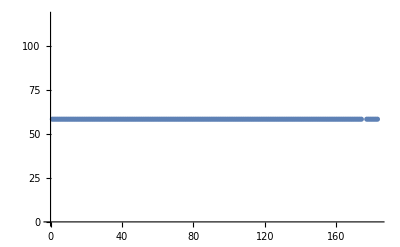

{Q220G,{{GGAATACACTATTGCCCATTAATGGGTATACAGAAAGCTCAGAAG,{45,40.,78.1381},1.16247,58.3501},{GAATACACTATTGCCCATTAATGGGTATACAGAAAGCTCAGAAG,{44,38.6364,77.2381},0.650563,58.3501},{CTGGAATACACTATTGCCCATTAATGGGTATACAGAAAGCTCAGAAGA,{48,39.5833,78.9048},0.412467,58.3501}}}

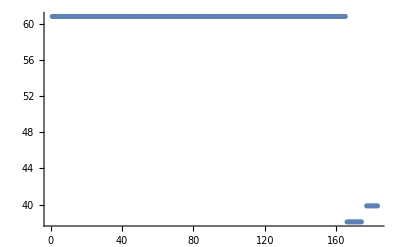

{Y245G,{{GTAAAAAAACACCTACATTCCCTGGTACAGATCTGGCTAAAGATTATG,{48,37.5,78.0506},0.797089,60.8116},{AGTAAAAAAACACCTACATTCCCTGGTACAGATCTGGCTAAAGATTATG,{49,36.7347,78.0238},-0.202911,60.8116},{GTAAAAAAACACCTACATTCCCTGGTACAGATCTGGCTAAAGATTATGA,{49,36.7347,78.0238},-0.202911,60.8116}}}

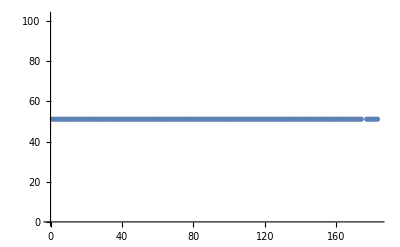

{G257A,{{GCTAAAGATTATGAAGCTAAAAAAGCATTAATCCGTACTACACCATTTG,{49,32.6531,78.7313},3.21884,51.1246},{CTAAAGATTATGAAGCTAAAAAAGCATTAATCCGTACTACACCATTTG,{48,31.25,77.869},3.08789,51.1246},{CTAAAGATTATGAAGCTAAAAAAGCATTAATCCGTACTACACCATTTGG,{49,32.6531,78.7313},2.96884,51.1246}}}

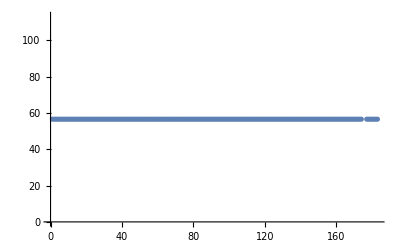

{T261G,{{GCTAAAAAAGGATTAATCCGTGGTACACCATTTGGAAATACCTTAACTC,{49,36.7347,78.0238},1.85032,56.5987},{GCTAAAAAAGGATTAATCCGTGGTACACCATTTGGAAATACCTTAAC,{47,36.1702,77.2062},1.0565,56.5987},{CTAAAAAAGGATTAATCCGTGGTACACCATTTGGAAATACCTTAACTC,{48,35.4167,77.1964},1.04675,56.5987}}}

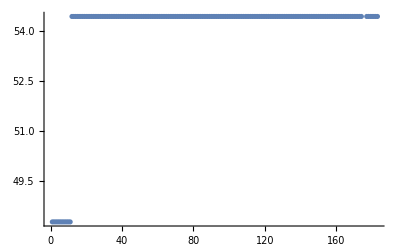

{T267G,{{GTACTACACCATTTGGAAATGGCTTAACTCTTCAGATGGCAG,{42,42.8571,78.2381},2.38756,54.4497},{CTACACCATTTGGAAATGGCTTAACTCTTCAGATGGCAGATG,{42,42.8571,78.2381},2.38756,54.4497},{CGTACTACACCATTTGGAAATGGCTTAACTCTTCAGATGGC,{41,43.9024,78.2747},2.13756,54.4497}}}

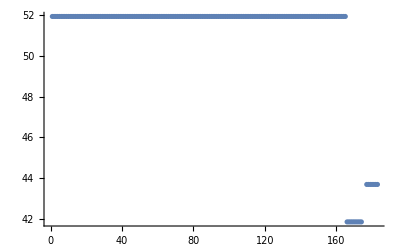

{D274G,{{CTCTTCAGATGGCAGGTGCTGCAATTGATGGTAAC,{35,48.5714,79.7476},3.01954,51.9219},{CTTAACTCTTCAGATGGCAGGTGCTGCAATTGATGG,{36,47.2222,79.7302},2.76954,51.9219},{CTCTTCAGATGGCAGGTGCTGCAATTGATGGTAACC,{36,50.,80.869},2.76954,51.9219}}}

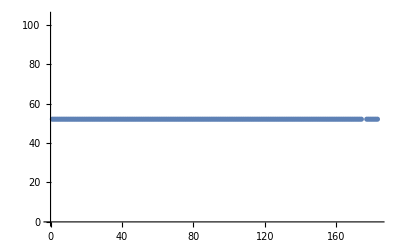

{A275G,{{CTCTTCAGATGGCAGATGGTGCAATTGATGGTAAC,{35,45.7143,78.5762},2.98369,52.0652},{CTCTTCAGATGGCAGATGGTGCAATTGATGGTAACC,{36,47.2222,79.7302},2.73369,52.0652},{CTTCAGATGGCAGATGGTGCAATTGATGGTAACC,{34,47.0588,78.5602},2.73369,52.0652}}}

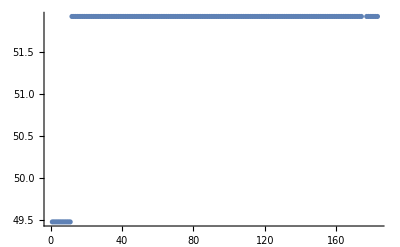

{I277G,{{CAGATGGCAGATGCTGCAGGTGATGGTAACCAAATG,{36,50.,78.4881},3.01954,51.9219},{GATGGCAGATGCTGCAGGTGATGGTAACCAAATGGGAG,{38,52.6316,80.5539},3.01954,51.9219},{GCAGATGCTGCAGGTGATGGTAACCAAATGGG,{32,53.125,77.4256},2.8076,49.472}}}

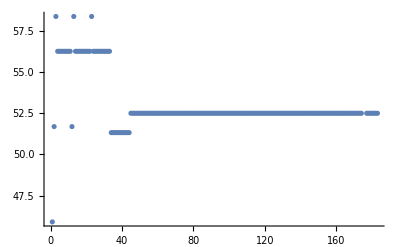

{D278G,{{GCAGATGCTGCAATTGGTGGTAACCAAATGGGAGTTG,{37,48.6486,80.8218},3.1695,51.322},{GCAGATGCTGCAATTGGTGGTAACCAAATGGGAG,{34,50.,79.7661},3.1695,51.322},{GCAGATGCTGCAATTGGTGGTAACCAAATGGG,{32,50.,78.5253},2.9195,51.322}}}

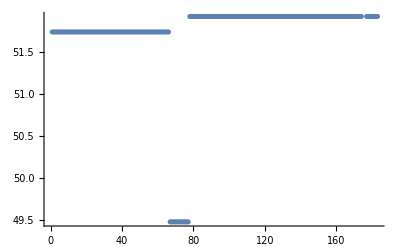

{G279A,{{GCAGATGCTGCAATTGATGCTAACCAAATGGGAGTTG,{37,45.9459,79.7136},3.632,49.472},{GCAGATGCTGCAATTGATGCTAACCAAATGGGAG,{34,47.0588,78.5602},3.632,49.472},{CAGATGCTGCAATTGATGCTAACCAAATGGGAGTTG,{36,44.4444,78.5913},3.06579,51.7368}}}

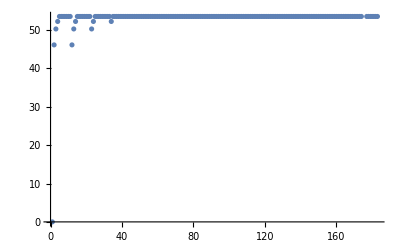

{N304G,{{CGGATTATGTTGGACACGGCTTTGGTCCAAACTCTATAG,{39,46.1538,78.3535},2.60979,53.5609},{CGGATTATGTTGGACACGGCTTTGGTCCAAACTC,{34,50.,77.3852},1.99494,53.5609},{GGATTATGTTGGACACGGCTTTGGTCCAAACTCTATAG,{38,44.7368,77.317},1.67683,53.5609}}}

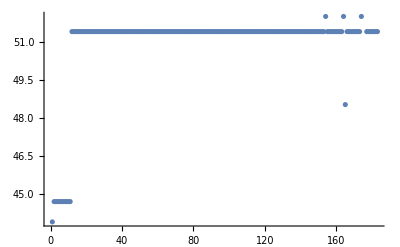

{F305G,{{CGGATTATGTTGGACACAACGGTGGTCCAAACTCTATAG,{39,46.1538,78.3535},3.1435,51.426},{GATTATGTTGGACACAACGGTGGTCCAAACTCTATAGAAGTTG,{43,41.8605,78.2032},3.1435,51.426},{GGATTATGTTGGACACAACGGTGGTCCAAACTCTATAGAAG,{41,43.9024,78.2747},2.8935,51.426}}}

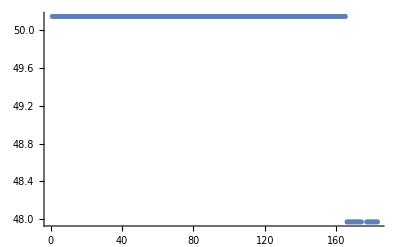

{I310G,{{CACAACTTTGGTCCAAACTCTGGAGAAGTTGAGGATACTTATC,{43,41.8605,78.2032},3.46365,50.1454},{CAACTTTGGTCCAAACTCTGGAGAAGTTGAGGATACTTATCTG,{43,41.8605,78.2032},3.46365,50.1454},{CTTTGGTCCAAACTCTGGAGAAGTTGAGGATACTTATCTG,{40,42.5,77.2881},2.75174,50.1454}}}

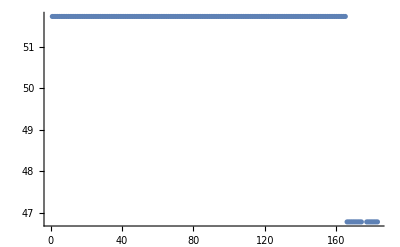

{E311G,{{CTTTGGTCCAAACTCTATAGGAGTTGAGGATACTTATCTG,{40,40.,78.644},3.06789,51.7284},{GGTCCAAACTCTATAGGAGTTGAGGATACTTATCTGAG,{38,42.1053,78.619},2.81789,51.7284},{CTTTGGTCCAAACTCTATAGGAGTTGAGGATACTTATC,{38,39.4737,77.5401},2.60799,51.7284}}}

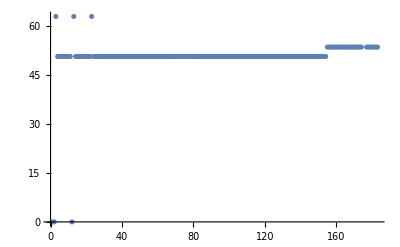

{V312G,{{GTCCAAACTCTATAGAAGGTGAGGATACTTATCTGAGATTAG,{42,38.0952,78.6667},3.32668,50.6933},{GGTCCAAACTCTATAGAAGGTGAGGATACTTATCTGAG,{38,42.1053,78.619},3.07668,50.6933},{GTCCAAACTCTATAGAAGGTGAGGATACTTATCTGAG,{37,40.5405,77.4974},2.82411,50.6933}}}

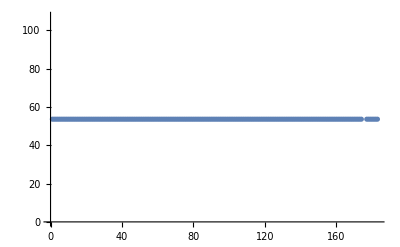

{Y316G,{{CTCTATAGAAGTTGAGGATACTGGTCTGAGATTAGACAGAGATTTG,{46,39.1304,78.1077},2.6056,53.5776},{CTCTATAGAAGTTGAGGATACTGGTCTGAGATTAGACAGAGATTTGG,{47,40.4255,78.9509},2.3556,53.5776},{CTATAGAAGTTGAGGATACTGGTCTGAGATTAGACAGAGATTTGGC,{46,41.3043,78.999},2.3556,53.5776}}}

-Graphics-

{L317G,{{CTATAGAAGTTGAGGATACTTATGGGAGATTAGACAGAGATTTGGCTG,{48,39.5833,78.9048},3.32668,50.6933},{GAAGTTGAGGATACTTATGGGAGATTAGACAGAGATTTGGCTG,{43,41.8605,78.2032},3.32668,50.6933},{CTCTATAGAAGTTGAGGATACTTATGGGAGATTAGACAGAGATTTGGC,{48,39.5833,78.9048},3.07668,50.6933}}}

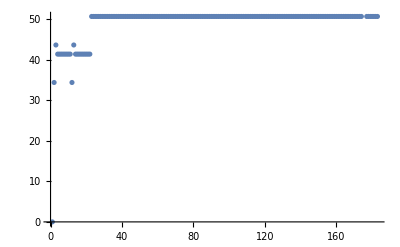

{R318G,{{GAGGATACTTATCTGGGATTAGACAGAGATTTGGCTG,{37,43.2432,78.6055},3.32668,50.6933},{GAAGTTGAGGATACTTATCTGGGATTAGACAGAGATTTGG,{40,40.,78.644},3.07668,50.6933},{GTTGAGGATACTTATCTGGGATTAGACAGAGATTTGGC,{38,42.1053,78.619},3.07668,50.6933}}}

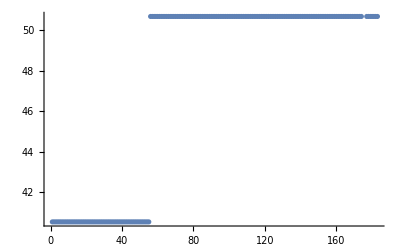

{L319G,{{GGATACTTATCTGAGAGGAGACAGAGATTTGGCTGACTTC,{40,45.,78.3131},3.75,40.5236},{GTTGAGGATACTTATCTGAGAGGAGACAGAGATTTGGCTG,{40,45.,78.3131},3.32668,50.6933},{GAGGATACTTATCTGAGAGGAGACAGAGATTTGGCTGAC,{39,46.1538,78.3535},3.32668,50.6933}}}

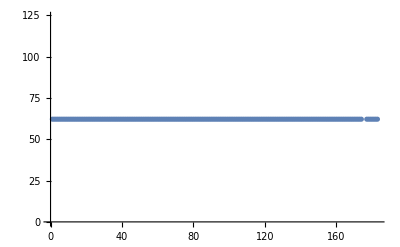

{G348A,{{CTTTCTGCGGATCATGCCGCTGCACATTCTGTG,{33,54.5455,81.0281},0.448024,62.2079},{CTTTCTGCGGATCATGCCGCTGCACATTCTG,{31,54.8387,79.8287},0.448024,62.2079},{CTTTCTGCGGATCATGCCGCTGCACATTC,{29,55.1724,78.4639},0.448024,62.2079}}}

-Graphics-

{S352G,{{GATCATGGCGCTGCACATGGTGTGGGCTTTATGCAAG,{37,54.0541,80.657},3.02411,51.9036},{CATGGCGCTGCACATGGTGTGGGCTTTATGCAAGCAC,{37,56.7568,81.7651},3.02411,51.9036},{CATGGCGCTGCACATGGTGTGGGCTTTATGCAAG,{34,55.8824,79.7969},3.02411,51.9036}}}

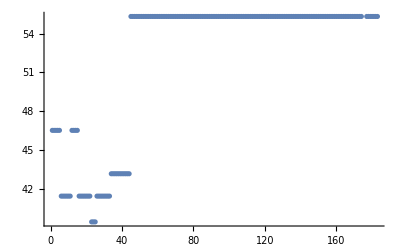

{F355G,{{GCACATTCTGTGGGCGGTATGCAAGCACATAAAATGCC,{38,50.,79.4749},3.75,43.1815},{GCACATTCTGTGGGCGGTATGCAAGCACATAAAATG,{36,47.2222,77.3492},3.34921,43.1815},{GCACATTCTGTGGGCGGTATGCAAGCACATAAAATGC,{37,48.6486,78.4408},3.25,43.1815}}}

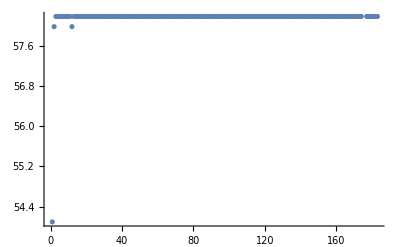

{M356G,{{CTGCACATTCTGTGGGCTTTGGGCAAGCACATAAAATG,{38,47.3684,78.396},1.4516,58.1936},{CATTCTGTGGGCTTTGGGCAAGCACATAAAATGCCAAC,{38,47.3684,78.396},1.4516,58.1936},{GCACATTCTGTGGGCTTTGGGCAAGCACATAAAATGCC,{38,50.,79.4749},1.2016,58.1936}}}

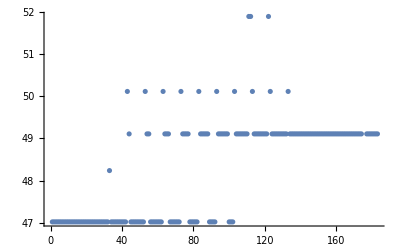

{Q357G,{{CACATTCTGTGGGCTTTATGGGAGCACATAAAATGCCAAC,{40,45.,78.3131},4.,47.0151},{CATTCTGTGGGCTTTATGGGAGCACATAAAATGCCAACAG,{40,45.,78.3131},3.47019,50.1193},{CATTCTGTGGGCTTTATGGGAGCACATAAAATGCCAAC,{38,44.7368,77.317},3.31704,47.0151}}}

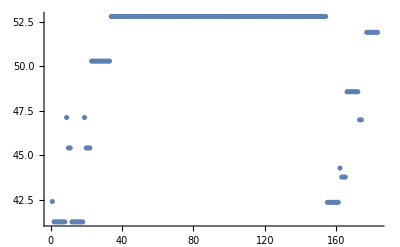

{H359G,{{CTGTGGGCTTTATGCAAGCAGGTAAAATGCCAACAGGC,{38,50.,79.4749},2.55162,52.7935},{GTGGGCTTTATGCAAGCAGGTAAAATGCCAACAGGC,{36,50.,78.4881},2.55162,52.7935},{GGGCTTTATGCAAGCAGGTAAAATGCCAACAGGCTTC,{37,48.6486,78.4408},2.55162,52.7935}}}

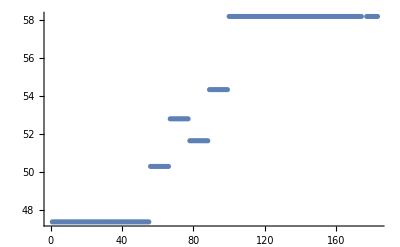

{K360G,{{GCTTTATGCAAGCACATGGAATGCCAACAGGCTTCTTTG,{39,46.1538,78.3535},3.42887,50.2845},{CTTTATGCAAGCACATGGAATGCCAACAGGCTTCTTTG,{38,44.7368,77.317},3.31704,47.358},{GGGCTTTATGCAAGCACATGGAATGCCAACAGGCTTC,{37,51.3514,79.5489},2.84069,51.6372}}}

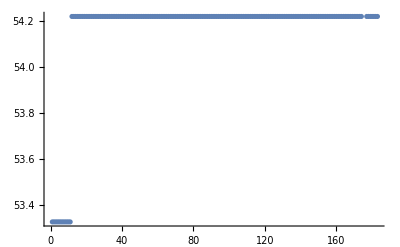

{V427G,{{GAACTTAAAAAAGAGCCATCAGGTCTTTATGTTCTTAGCACG,{42,38.0952,78.6667},2.19543,54.2183},{CTTAAAAAAGAGCCATCAGGTCTTTATGTTCTTAGCACGG,{40,40.,78.644},2.19543,54.2183},{GAACTTAAAAAAGAGCCATCAGGTCTTTATGTTCTTAGCAC,{41,36.5854,77.6556},2.10107,54.2183}}}

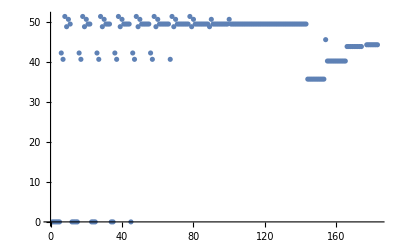

{S432G,{{GTTCTTTATGTTCTTGGCACGGATGAAATCTGGGAATC,{38,42.1053,78.619},3.64203,49.4319},{CATCAGTTCTTTATGTTCTTGGCACGGATGAAATCTGG,{38,42.1053,78.619},3.5581,48.7676},{CAGTTCTTTATGTTCTTGGCACGGATGAAATCTGGG,{36,44.4444,78.5913},3.09852,50.6059}}}

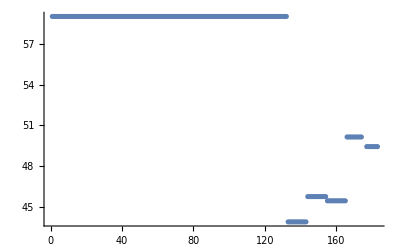

{P442G,{{GATGAAATCTGGGAATCGTCTATTGGGGAACCGATAAAGTCCAGAG,{46,45.6522,80.7816},2.16,43.8805},{CTGGGAATCGTCTATTGGGGAACCGATAAAGTCCAGAG,{38,50.,79.4749},1.24273,59.0291},{CTGGGAATCGTCTATTGGGGAACCGATAAAGTCCAG,{36,50.,78.4881},1.24273,59.0291}}}

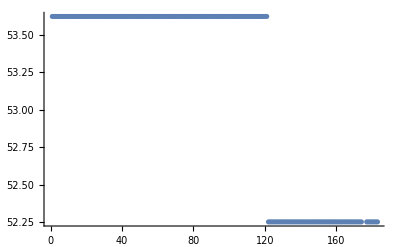

{I445G,{{CGTCTATTCCGGAACCGGGAAAGTCCAGAGTAATC,{35,51.4286,78.5381},2.594,53.624},{GTCTATTCCGGAACCGGGAAAGTCCAGAGTAATCAATG,{38,47.3684,78.396},2.594,53.624},{GTCTATTCCGGAACCGGGAAAGTCCAGAGTAATC,{34,50.,77.3852},1.97916,53.624}}}

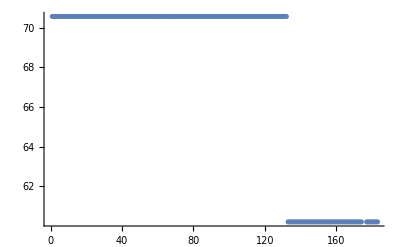

{K446G,{{GTCTATTCCGGAACCGATAGGGTCCAGAGTAATCAATG,{38,47.3684,78.396},-1.64002,70.5601},{CTATTCCGGAACCGATAGGGTCCAGAGTAATCAATGG,{37,48.6486,78.4408},-1.89002,70.5601},{GAATCGTCTATTCCGGAACCGATAGGGTCCAGAGTAATCAATGGTT,{46,45.6522,80.7816},-2.14278,60.2111}}}

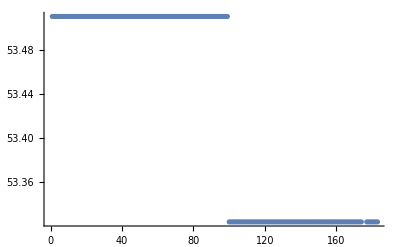

{Y469G,{{CAGATCATTTCTAAAGACGGAGGTCTTTCAGCATATTCCAAAAAAGGG,{48,39.5833,78.9048},2.41892,53.3243},{CAGATCATTTCTAAAGACGGAGGTCTTTCAGCATATTCCAAAAAAGG,{47,38.2979,78.0785},2.41892,53.3243},{GATCATTTCTAAAGACGGAGGTCTTTCAGCATATTCCAAAAAAGGG,{46,39.1304,78.1077},2.37251,53.51}}}

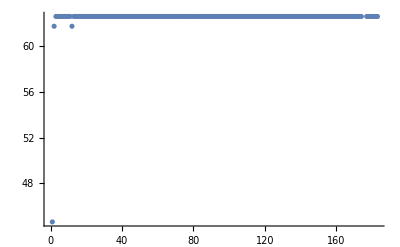

{S504G,{{GTATCAAACAGGGAGAGGGCAATCAGCCATACCATATG,{38,47.3684,78.396},0.356816,62.5727},{GGTATCAAACAGGGAGAGGGCAATCAGCCATACC,{34,52.9412,78.591},-0.143184,62.5727},{CAAACAGGGAGAGGGCAATCAGCCATACCATATG,{34,50.,77.3852},-0.25803,62.5727}}}

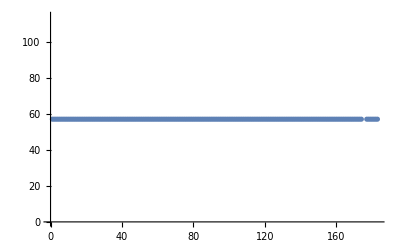

{P515G,{{GCCATACCATATGACGGATATTGCAGGAACTGTTTCATCATTACTTAAA,{49,36.7347,78.0238},0.48293,57.0683},{GCCATACCATATGACGGATATTGCAGGAACTGTTTCATCATTACTTAA,{48,37.5,78.0506},0.48293,57.0683},{CCATACCATATGACGGATATTGCAGGAACTGTTTCATCATTACTTA,{46,36.9565,77.2164},-0.550714,57.0683}}}

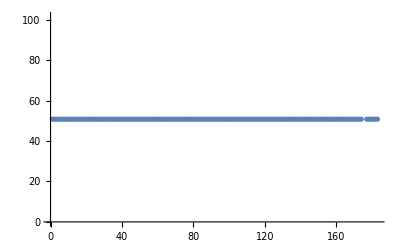

{S518G,{{GACGGATATTGCACCAACTGTTGGATCATTACTTAAAATTCAGTTCCC,{48,39.5833,78.9048},3.04345,50.8262},{GACGGATATTGCACCAACTGTTGGATCATTACTTAAAATTCAGTTCC,{47,38.2979,78.0785},3.04345,50.8262},{CGGATATTGCACCAACTGTTGGATCATTACTTAAAATTCAGTTCCC,{46,39.1304,78.1077},3.04345,50.8262}}}

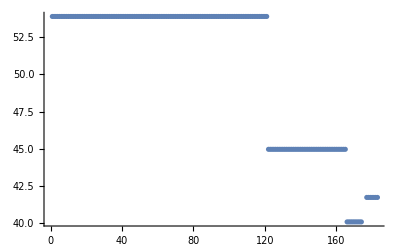

{P533G,{{CTAGTGGTGCTGTAGGTAAAGGAATTACCGAAGTTATAGGAAG,{43,41.8605,78.2032},2.53137,53.8745},{GTGGTGCTGTAGGTAAAGGAATTACCGAAGTTATAGGAAGAG,{42,42.8571,78.2381},2.53137,53.8745},{GTTCCCTAGTGGTGCTGTAGGTAAAGGAATTACCGAAGTTATAGGAAG,{48,43.75,80.6131},2.08,44.9678}}}

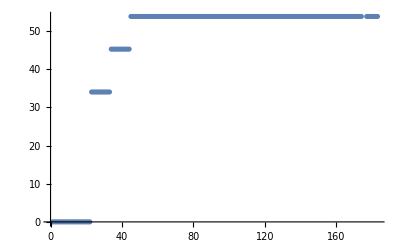

{E536G,{{GTAAACCAATTACCGGAGTTATAGGAAGAGGAGGAG,{36,44.4444,78.5913},4.,34.0655},{GGTAAACCAATTACCGGAGTTATAGGAAGAGGAGGAG,{37,45.9459,79.7136},3.75,45.3046},{GGTAAACCAATTACCGGAGTTATAGGAAGAGGAGGAGG,{38,47.3684,80.7769},3.5,45.3046}}}

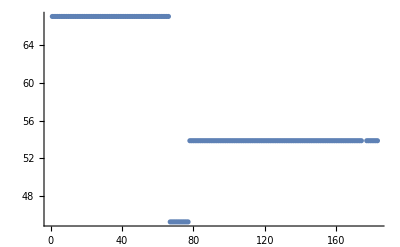

{V537G,{{GGTAAACCAATTACCGAAGGTATAGGAAGAGGAGGAG,{37,45.9459,79.7136},3.75,45.3046},{GGTAAACCAATTACCGAAGGTATAGGAAGAGGAGGAGG,{38,47.3684,80.7769},3.5,45.3046},{GGTAAACCAATTACCGAAGGTATAGGAAGAGGAGG,{35,45.7143,78.5762},3.5,45.3046}}}

```mathematica
Dynamic[loop]
Dynamic[i]

Do[

resnumber=ToExpression[StringDrop[StringDrop[mutation[[loop]],{1}],{-1}]];

restypeIN=StringTake[mutation[[loop]],{-1}];

(* calculate the number of base pair changes between the wild-type sequence and all codons of the mutated amino acid *)
newrescodons=Which[restypeIN=="A",alanine,restypeIN=="G",glycine,restypeIN=="D",aspartate,restypeIN=="N",asparagine,restypeIN=="E",glutamate,restypeIN=="Q",glutamine,restypeIN=="V",valine,restypeIN=="L",leucine,restypeIN=="I",isoleucine,restypeIN=="P",proline,restypeIN=="H",histidine,restypeIN=="K",lysine,restypeIN=="R",arginine,restypeIN=="Y",tyrosine,restypeIN=="F",phenylalanine,restypeIN=="W",tryptophan,restypeIN=="S",serine,restypeIN=="T",threonine,restypeIN=="C",cysteine,restypeIN=="M",methionine];

testwt=pafAcodons[[resnumber]];
(*Print[testwt];

Print[translation[[resnumber]]];*)

Do[

testmutant=Characters[newrescodons[[i]]];

codondiff[i]=If[testwt[[1]]==testmutant[[1]],0,1]+If[testwt[[2]]==testmutant[[2]],0,1]+If[testwt[[3]]==testmutant[[3]],0,1];

,{i,1,Length[newrescodons]}];

(* select codon requiring the least number of base pair changes *)
newcodon=Sort[Table[{StringJoin[newrescodons[[i]]],codondiff[i]},{i,1,Length[newrescodons]}],#1[[2]]<#2[[2]]&][[1]];

(*Print["New codon"];
Print[newcodon];*)

(* test a range of flanking lengths *)
base5prime=resnumber*3-2;
base3prime=resnumber*3;

(* below plots the piecewise function used by Tmscore *)
(* Plot[Piecewise[{{2,Tm≥78.0},{(Tm-77.0)+1,Tm≥77.0},{(Tm-70.0)*0.142857,Tm<77.0}}],{Tm,70,85}] *)

(* counter for indexing the mutagenic primers *)
counter=0;

Do[

Do[

fiveprimeend=base5prime-i;
threeprimeend=base3prime+j;

wildtypeprimer=StringTake[pafAsequence,{fiveprimeend,threeprimeend}];

(* insert mutation into sense primer *)
mutagenicprimer=StringJoin[StringTake[pafAsequence,{fiveprimeend,base5prime-1}],StringJoin[newcodon[[1]]],StringTake[pafAsequence,{base3prime+1,threeprimeend}]];

gcfirst=If[StringTake[mutagenicprimer,1]=="G"||StringTake[mutagenicprimer,1]=="C",1,0];

gclast=If[StringTake[mutagenicprimer,-1]=="G"||StringTake[mutagenicprimer,-1]=="C",1,0];

(* calculate the annealing portion of the sequence for Tm calcuations *)
wtseq=Characters[wildtypeprimer];
mutantseq=Characters[mutagenicprimer];

seqforTm=StringJoin[Select[Table[If[wtseq[[i]]==mutantseq[[i]],wtseq[[i]]],{i,1,Length[wtseq]}],#=="G"||#=="C"||#=="A"||#=="T"&]];

(* use "primerparams" function to calculate %GC and melting temperature *)
parameters=primerparams[mutagenicprimer,seqforTm,newcodon[[2]]];

(* include penalties for primer 3' self-complementarity *)
onebase=If[getcomplement[StringTake[mutagenicprimer,-1]]==StringTake[mutagenicprimer,{-2}],-0.25,0];
twobases=If[getcomplement[StringTake[mutagenicprimer,{2}]]==StringTake[mutagenicprimer,{-2}]&&onebase==-0.25,-0.5,0];
threebases=If[getcomplement[StringTake[mutagenicprimer,{3}]]==StringTake[mutagenicprimer,{-3}]&&twobases==-0.25,-1.0,0];

(* hairpin penalty function *)
hairpin=Piecewise[{{0,hTm<48.0},{-0.25*hTm+0.25*48.0,hTm≥48.0}}];

hairpinTm=ToExpression[calcHairpin[mutagenicprimer]];

(* calculate final "objective function" score *)
(* 06/24/26 - included a penalty for longer primers (to reduce oligo synthesis costs) *)
endscore=gcfirst+gclast+Tmscore[parameters[[3]]]+If[StringLength[mutagenicprimer]>19*2&&parameters[[3]]>79.0,(-0.04*StringLength[mutagenicprimer]),0]+If[StringTake[mutagenicprimer,{-1}]==StringTake[mutagenicprimer,{-2}],-0.25,0.0]+If[StringTake[mutagenicprimer,{1}]==StringTake[mutagenicprimer,{2}],-0.25,0.0]+onebase+twobases+threebases+(hairpin/.{hTm->hairpinTm});

(* need to clear the self-complementarity tests otherwise will be included in calculations for subsequent primers *)
Clear[onebase,twobases,threebases];

(* counter *)
counter2=counter+1;
counter=counter2;

primertest[counter]={mutagenicprimer,parameters,endscore,hairpinTm};

,{j,i-5,i+5}]

,{i,12,28}];

allprimers=Table[primertest[m],{m,1,counter}];

(*Print[allprimers];*)

Print[ListPlot[allprimers[[All,4]],PlotRange->All]];

best[mutation[[loop]]]={mutation[[loop]],Select[Sort[allprimers,#1[[3]]>#2[[3]]&],#[[2,1]]<50&][[1;;3]]};

Print[best[mutation[[loop]]]];

,{loop,1,Length[mutation]}]
```

```mathematica
mutationproperresnums=Table[StringJoin[StringTake[mutation[[n]],1],ToString[ToExpression[StringDrop[StringDrop[mutation[[n]],-1],1]]+6],StringTake[mutation[[n]],-1]],{n,1,Length[mutation]}];
```

```mathematica
Dynamic[n]

primers=Table[{ToExpression[StringDrop[StringDrop[mutation[[n]],-1],1]]+6,mutationproperresnums[[n]],best[mutation[[n]]][[2,1,1]],"","","","","",reversecomplement[best[mutation[[n]]][[2,1,1]]],ToExpression[calcHairpin[best[mutation[[n]]][[2,1,1]]]]},{n,1,Length[mutation]}];
```

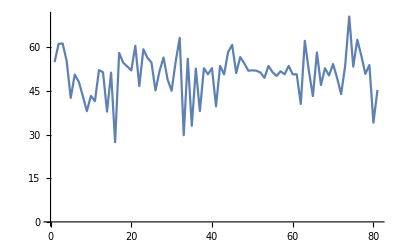

```mathematica
ListPlot[Select[primers,#[[10]]>1&][[All,10]],Joined->True]
```

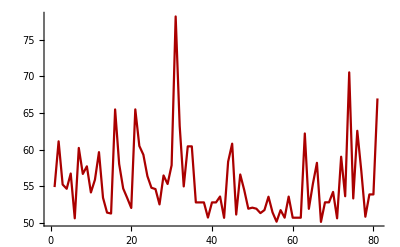
```mathematica
Show[-Graphics-,-Graphics-,PlotRange->All]
```

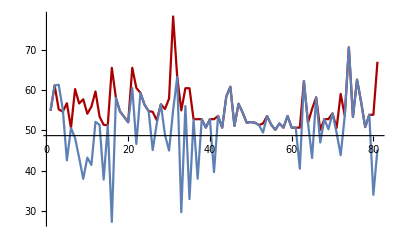

```mathematica
primers
```

{{53,G53A,CCGTTATTATAGCAAGTATGCTGAAGGAGGTTTTAAGAGAATG,,,,,,CATTCTCTTAAAACCTCCTTCAGCATACTTGCTATAATAACGG,54.8795},{62,N62G,GAGGTTTTAAGAGAATGCTGGGTACCGGGTATTCGTTAAATAATGTTC,,,,,,GAACATTATTTAACGAATACCCGGTACCCAGCATTCTCTTAAAACCTC,61.1327},{78,V78G,GACTATGTACCTACAGGAACTGCAATCGGACATACTTC,,,,,,GAAGTATGTCCGATTGCAGTTCCTGTAGGTACATAGTC,61.2989},{79,T79G,GACTATGTACCTACAGTAGGTGCAATCGGACATACTTC,,,,,,GAAGTATGTCCGATTGCACCTACTGTAGGTACATAGTC,55.2256},{88,T88G,CGGACATACTTCAATTTTTGGAGGTTCTGTTCCCTC,,,,,,GAGGGAACAGAACCTCCAAAAATTGAAGTATGTCCG,42.5915},{93,S93G,CAGGTTCTGTTCCCGGCATCCACGGAATTGCAG,,,,,,CTGCAATTCCGTGGATGCCGGGAACAGAACCTG,50.6077},{94,I94G,ACAGGTTCTGTTCCCTCCGGCCACGGAATTGCAG,,,,,,CTGCAATTCCGTGGCCGGAGGGAACAGAACCTGT,48.1208},{97,I97G,CTCCATCCACGGAGGTGCAGGAAACGATTGG,,,,,,CCAATCGTTTCCTGCACCTCCGTGGATGGAG,43.2489},{122,V122G,CTGATGAAACAGTACAACCGGGAGGAACTACTTCTAAC,,,,,,GTTAGAAGTAGTTCCTCCCGGTTGTACTGTTTCATCAG,38.0342},{124,T124G,CAGTACAACCGGTAGGAGGTACTTCTAACTCGG,,,,,,CCGAGTTAGAAGTACCTCCTACCGGTTGTACTG,43.2902},{125,T125G,CCGGTAGGAACTGGTTCTAACTCGGTTGGAC,,,,,,GTCCAACCGAGTTAGAACCAGTTCCTACCGG,41.475},{126,S126G,CGGTAGGAACTACTGGTAACTCGGTTGGACAAC,,,,,,GTTGTCCAACCGAGTTACCAGTAGTTCCTACCG,52.1271},{127,N127G,GTAGGAACTACTTCTGGCTCGGTTGGACAACATTCAC,,,,,,GTGAATGTTGTCCAACCGAGCCAGAAGTAGTTCCTAC,51.39},{128,S128G,GGAACTACTTCTAACGGGGTTGGACAACATTCACCAAG,,,,,,CTTGGTGAATGTTGTCCAACCCCGTTAGAAGTAGTTCC,37.8679},{138,W138G,CATTCACCAAGAAACCTTGGGTCTACTACGGTAACAG,,,,,,CTGTTACCGTAGTAGACCCAAGGTTTCTTGGTGAATG,51.2646},{145,Q145G,GTCTACTACGGTAACAGATGGGCTAGGTTTGGCAAC,,,,,,GTTGCCAAACCTAGCCCATCTGTTACCGTAGTAGAC,27.3743},{146,L146G,CTACGGTAACAGATCAGGGAGGTTTGGCAACAAACTTTAC,,,,,,GTAAAGTTTGTTGCCAAACCTCCCTGATCTGTTACCGTAG,58.037},{147,G147A,CGGTAACAGATCAGCTAGCTTTGGCAACAAACTTTAC,,,,,,GTAAAGTTTGTTGCCAAAGCTAGCTGATCTGTTACCG,54.6857},{149,A149G,GTAACAGATCAGCTAGGTTTGGGAACAAACTTTACTTCTAAG,,,,,,CTTAGAAGTAAAGTTTGTTCCCAAACCTAGCTGATCTGTTAC,53.3855},{151,N151G,GATCAGCTAGGTTTGGCAACAGGCTTTACTTCTAAGGTTG,,,,,,CAACCTTAGAAGTAAAGCCTGTTGCCAAACCTAGCTGATC,52.02},{152,F152G,GTTTGGCAACAAACGGTACTTCTAAGGTTGTGGGGG,,,,,,CCCCCACAACCTTAGAAGTACCGTTTGTTGCCAAAC,60.4986},{153,T153G,GGCAACAAACTTTGGTTCTAAGGTTGTGGGGGTC,,,,,,GACCCCCACAACCTTAGAACCAAAGTTTGTTGCC,46.6533},{160,S160G,CTAAGGTTGTGGGGGTCGGTCTGAAAGACAGAGCATC,,,,,,GATGCTCTGTCTTTCAGACCGACCCCCACAACCTTAG,59.3018},{162,K162G,GTTGTGGGGGTCTCTCTGGGAGACAGAGCATCAATTC,,,,,,GAATTGATGCTCTGTCTCCCAGAGAGACCCCCACAAC,56.3738},{163,D163G,GTGGGGGTCTCTCTGAAAGGCAGAGCATCAATTC,,,,,,GAATTGATGCTCTGCCTTTCAGAGAGACCCCCAC,54.7844},{165,A165G,CTGAAAGACAGAGGATCAATTCTGCCTGCAGG,,,,,,CCTGCAGGCAGAATTGATCCTCTGTCTTTCAG,45.1337},{166,S166G,CTGAAAGACAGAGCAGGAATTCTGCCTGCAGGGCAC,,,,,,GTGCCCTGCAGGCAGAATTCCTGCTCTGTCTTTCAG,51.7626},{167,I167G,CTGAAAGACAGAGCATCAGGTCTGCCTGCAGGGCAC,,,,,,GTGCCCTGCAGGCAGACCTGATGCTCTGTCTTTCAG,56.4682},{168,L168G,GACAGAGCATCAATTGGGCCTGCAGGGCAC,,,,,,GTGCCCTGCAGGCCCAATTGATGCTCTGTC,48.9282},{170,A170G,GAGCATCAATTCTGCCTGGAGGGCACAACCCAAC,,,,,,GTTGGGTTGTGCCCTCCAGGCAGAATTGATGCTC,45.0226},{172,H172G,GAGCATCAATTCTGCCTGCAGGGGGCAACCCAACAGGAGCATTTTG,,,,,,CAAAATGCTCCTGTTGGGTTGCCCCCTGCAGGCAGAATTGATGCTC,55.0191},{173,N173G,CTGCCTGCAGGGCACGGCCCAACAGGAG,,,,,,CTCCTGTTGGGCCGTGCCCTGCAGGCAG,63.2106},{174,P174G,CTGCAGGGCACAACGGAACAGGAGCATTTTGGTTC,,,,,,GAACCAAAATGCTCCTGTTCCGTTGTGCCCTGCAG,29.7673},{175,T175G,GGGCACAACCCAGGAGGAGCATTTTGGTTC,,,,,,GAACCAAAATGCTCCTCCTGGGTTGTGCCC,56.0525},{176,G176A,GCACAACCCAACAGCAGCATTTTGGTTCGATG,,,,,,CATCGAACCAAAATGCTGCTGTTGGGTTGTGC,33.0035},{183,T183G,GAGCATTTTGGTTCGATGATGGTACAGGTAAATTCATTACCAGTAC,,,,,,GTACTGGTAATGAATTTACCTGTACCATCATCGAACCAAAATGCTC,52.6555},{184,T184G,AGGAGCATTTTGGTTCGATGATACTGGAGGTAAATTCATTACCAGTAC,,,,,,GTACTGGTAATGAATTTACCTCCAGTATCATCGAACCAAAATGCTCCT,38.0667},{187,F187G,GGTTCGATGATACTACAGGTAAAGGCATTACCAGTACATATTATAC,,,,,,GTATAATATGTACTGGTAATGCCTTTACCTGTAGTATCATCGAACC,52.7829},{190,S190G,GATACTACAGGTAAATTCATTACCGGTACATATTATACTAAAGAATTAC,,,,,,GTAATTCTTTAGTATAATATGTACCGGTAATGAATTTACCTGTAGTATC,50.7092},{191,T191G,CTACAGGTAAATTCATTACCAGTGGATATTATACTAAAGAATTACC,,,,,,GGTAATTCTTTAGTATAATATCCACTGGTAATGAATTTACCTGTAG,52.7829},{192,Y192G,GTAAATTCATTACCAGTACAGGTTATACTAAAGAATTACCTAAATGGG,,,,,,CCCATTTAGGTAATTCTTTAGTATAACCTGTACTGGTAATGAATTTAC,39.6777},{195,K195G,CATTACCAGTACATATTATACTGGAGAATTACCTAAATGGGTAAACGAC,,,,,,GTCGTTTACCCATTTAGGTAATTCTCCAGTATAATATGTACTGGTAATG,53.5885},{214,V214G,GTTCCGGCTCAGTTGGGAGCTAATGGCTG,,,,,,CAGCCATTAGCTCCCAACTGAGCCGGAAC,50.6759},{226,Q226G,GGAATACACTATTGCCCATTAATGGGTATACAGAAAGCTCAGAAG,,,,,,CTTCTGAGCTTTCTGTATACCCATTAATGGGCAATAGTGTATTCC,58.3501},{251,Y251G,GTAAAAAAACACCTACATTCCCTGGTACAGATCTGGCTAAAGATTATG,,,,,,CATAATCTTTAGCCAGATCTGTACCAGGGAATGTAGGTGTTTTTTTAC,60.8116},{263,G263A,GCTAAAGATTATGAAGCTAAAAAAGCATTAATCCGTACTACACCATTTG,,,,,,CAAATGGTGTAGTACGGATTAATGCTTTTTTAGCTTCATAATCTTTAGC,51.1246},{267,T267G,GCTAAAAAAGGATTAATCCGTGGTACACCATTTGGAAATACCTTAACTC,,,,,,GAGTTAAGGTATTTCCAAATGGTGTACCACGGATTAATCCTTTTTTAGC,56.5987},{273,T273G,GTACTACACCATTTGGAAATGGCTTAACTCTTCAGATGGCAG,,,,,,CTGCCATCTGAAGAGTTAAGCCATTTCCAAATGGTGTAGTAC,54.4497},{280,D280G,CTCTTCAGATGGCAGGTGCTGCAATTGATGGTAAC,,,,,,GTTACCATCAATTGCAGCACCTGCCATCTGAAGAG,51.9219},{281,A281G,CTCTTCAGATGGCAGATGGTGCAATTGATGGTAAC,,,,,,GTTACCATCAATTGCACCATCTGCCATCTGAAGAG,52.0652},{283,I283G,CAGATGGCAGATGCTGCAGGTGATGGTAACCAAATG,,,,,,CATTTGGTTACCATCACCTGCAGCATCTGCCATCTG,51.9219},{284,D284G,GCAGATGCTGCAATTGGTGGTAACCAAATGGGAGTTG,,,,,,CAACTCCCATTTGGTTACCACCAATTGCAGCATCTGC,51.322},{285,G285A,GCAGATGCTGCAATTGATGCTAACCAAATGGGAGTTG,,,,,,CAACTCCCATTTGGTTAGCATCAATTGCAGCATCTGC,49.472},{310,N310G,CGGATTATGTTGGACACGGCTTTGGTCCAAACTCTATAG,,,,,,CTATAGAGTTTGGACCAAAGCCGTGTCCAACATAATCCG,53.5609},{311,F311G,CGGATTATGTTGGACACAACGGTGGTCCAAACTCTATAG,,,,,,CTATAGAGTTTGGACCACCGTTGTGTCCAACATAATCCG,51.426},{316,I316G,CACAACTTTGGTCCAAACTCTGGAGAAGTTGAGGATACTTATC,,,,,,GATAAGTATCCTCAACTTCTCCAGAGTTTGGACCAAAGTTGTG,50.1454},{317,E317G,CTTTGGTCCAAACTCTATAGGAGTTGAGGATACTTATCTG,,,,,,CAGATAAGTATCCTCAACTCCTATAGAGTTTGGACCAAAG,51.7284},{318,V318G,GTCCAAACTCTATAGAAGGTGAGGATACTTATCTGAGATTAG,,,,,,CTAATCTCAGATAAGTATCCTCACCTTCTATAGAGTTTGGAC,50.6933},{322,Y322G,CTCTATAGAAGTTGAGGATACTGGTCTGAGATTAGACAGAGATTTG,,,,,,CAAATCTCTGTCTAATCTCAGACCAGTATCCTCAACTTCTATAGAG,53.5776},{323,L323G,CTATAGAAGTTGAGGATACTTATGGGAGATTAGACAGAGATTTGGCTG,,,,,,CAGCCAAATCTCTGTCTAATCTCCCATAAGTATCCTCAACTTCTATAG,50.6933},{324,R324G,GAGGATACTTATCTGGGATTAGACAGAGATTTGGCTG,,,,,,CAGCCAAATCTCTGTCTAATCCCAGATAAGTATCCTC,50.6933},{325,L325G,GGATACTTATCTGAGAGGAGACAGAGATTTGGCTGACTTC,,,,,,GAAGTCAGCCAAATCTCTGTCTCCTCTCAGATAAGTATCC,40.5236},{354,G354A,CTTTCTGCGGATCATGCCGCTGCACATTCTGTG,,,,,,CACAGAATGTGCAGCGGCATGATCCGCAGAAAG,62.2079},{358,S358G,GATCATGGCGCTGCACATGGTGTGGGCTTTATGCAAG,,,,,,CTTGCATAAAGCCCACACCATGTGCAGCGCCATGATC,51.9036},{361,F361G,GCACATTCTGTGGGCGGTATGCAAGCACATAAAATGCC,,,,,,GGCATTTTATGTGCTTGCATACCGCCCACAGAATGTGC,43.1815},{362,M362G,CTGCACATTCTGTGGGCTTTGGGCAAGCACATAAAATG,,,,,,CATTTTATGTGCTTGCCCAAAGCCCACAGAATGTGCAG,58.1936},{363,Q363G,CACATTCTGTGGGCTTTATGGGAGCACATAAAATGCCAAC,,,,,,GTTGGCATTTTATGTGCTCCCATAAAGCCCACAGAATGTG,47.0151},{365,H365G,CTGTGGGCTTTATGCAAGCAGGTAAAATGCCAACAGGC,,,,,,GCCTGTTGGCATTTTACCTGCTTGCATAAAGCCCACAG,52.7935},{366,K366G,GCTTTATGCAAGCACATGGAATGCCAACAGGCTTCTTTG,,,,,,CAAAGAAGCCTGTTGGCATTCCATGTGCTTGCATAAAGC,50.2845},{433,V433G,GAACTTAAAAAAGAGCCATCAGGTCTTTATGTTCTTAGCACG,,,,,,CGTGCTAAGAACATAAAGACCTGATGGCTCTTTTTTAAGTTC,54.2183},{438,S438G,GTTCTTTATGTTCTTGGCACGGATGAAATCTGGGAATC,,,,,,GATTCCCAGATTTCATCCGTGCCAAGAACATAAAGAAC,49.4319},{448,P448G,GATGAAATCTGGGAATCGTCTATTGGGGAACCGATAAAGTCCAGAG,,,,,,CTCTGGACTTTATCGGTTCCCCAATAGACGATTCCCAGATTTCATC,43.8805},{451,I451G,CGTCTATTCCGGAACCGGGAAAGTCCAGAGTAATC,,,,,,GATTACTCTGGACTTTCCCGGTTCCGGAATAGACG,53.624},{452,K452G,GTCTATTCCGGAACCGATAGGGTCCAGAGTAATCAATG,,,,,,CATTGATTACTCTGGACCCTATCGGTTCCGGAATAGAC,70.5601},{475,Y475G,CAGATCATTTCTAAAGACGGAGGTCTTTCAGCATATTCCAAAAAAGGG,,,,,,CCCTTTTTTGGAATATGCTGAAAGACCTCCGTCTTTAGAAATGATCTG,53.3243},{510,S510G,GTATCAAACAGGGAGAGGGCAATCAGCCATACCATATG,,,,,,CATATGGTATGGCTGATTGCCCTCTCCCTGTTTGATAC,62.5727},{521,P521G,GCCATACCATATGACGGATATTGCAGGAACTGTTTCATCATTACTTAAA,,,,,,TTTAAGTAATGATGAAACAGTTCCTGCAATATCCGTCATATGGTATGGC,57.0683},{524,S524G,GACGGATATTGCACCAACTGTTGGATCATTACTTAAAATTCAGTTCCC,,,,,,GGGAACTGAATTTTAAGTAATGATCCAACAGTTGGTGCAATATCCGTC,50.8262},{539,P539G,CTAGTGGTGCTGTAGGTAAAGGAATTACCGAAGTTATAGGAAG,,,,,,CTTCCTATAACTTCGGTAATTCCTTTACCTACAGCACCACTAG,53.8745},{542,E542G,GTAAACCAATTACCGGAGTTATAGGAAGAGGAGGAG,,,,,,CTCCTCCTCTTCCTATAACTCCGGTAATTGGTTTAC,34.0655},{543,V543G,GGTAAACCAATTACCGAAGGTATAGGAAGAGGAGGAG,,,,,,CTCCTCCTCTTCCTATACCTTCGGTAATTGGTTTACC,45.3046}}